#### Solve for Gaussian Normal coordinate

```mathematica
DSolve[w'[z]==l^2/z^2 1/(1-z^4/zh^4),w[z],z]
```

{{w[z]→C[1]+l^2 zh^4 (-1/(z zh^4)-ArcTan[z/zh]/(2 zh^5)-Log[-z+zh]/(4 zh^5)+Log[z+zh]/(4 zh^5))}}

```mathematica
DSolve[w'[z]==l/z 1/(√(1-z^4/zh^4)),w[z],z]
```

{{w[z]→-1/2 l ArcTanh[√(1-z^4/zh^4)]+C[1]}}

```mathematica
wofz=-1/2 l ArcTanh[√(1-z^4/zh^4)]
```

-1/2 l ArcTanh[√(1-z^4/zh^4)]

```mathematica
Simplify[Solve[-1/2 l ArcTanh[√(1-z^4/zh^4)]==w,z]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{z→-(zh^4 Sech[(2 w)/l]^2)^(1/4)},{z→-ⅈ (zh^4 Sech[(2 w)/l]^2)^(1/4)},{z→ⅈ (zh^4 Sech[(2 w)/l]^2)^(1/4)},{z→(zh^4 Sech[(2 w)/l]^2)^(1/4)}}

take positive real root

```mathematica
Simplify[z==zh(1 - Tanh[(- 2 w)/l]^2)^(1/4)]
```

z==zh (Sech[(2 w)/l]^2)^(1/4)

```mathematica
zh Abs[Sech[2 w/l]]^(1/2)
```

zh √Abs[Sech[(2 w)/l]]

```mathematica
zofw=Simplify[TrigToExp[zh √Sech[(2 w)/l]]]
```

√2 √(1/(ⅇ^(-(2 w)/l)+ⅇ^((2 w)/l))) zh

#### Compute metric

```mathematica
ds = l^2/z^2(-(1-z^4/zh^4)dt^2+dx^2)+dw^2
ds/.z->zofw
dsofw =FullSimplify[%]
```

dw^2+(l^2 (dx^2+dt^2 (-1+z^4/zh^4)))/z^2

dw^2+((ⅇ^(-(2 w)/l)+ⅇ^((2 w)/l)) (dx^2+dt^2 (-1+4/((ⅇ^(-(2 w)/l)+ⅇ^((2 w)/l))^2))) l^2)/(2 zh^2)

dw^2+(l^2 (dt^2+(-dt^2+dx^2) Cosh[(2 w)/l]^2) Sech[(2 w)/l])/zh^2

```mathematica
D[wofz,z]^2
```

l^2/(z^2 (1-z^4/zh^4))

```mathematica
FullSimplify[l^2/z^2(1-z^4/zh^4)/.z->zofw]
D[%,w]
```

(l^2 Sinh[(2 w)/l] Tanh[(2 w)/l])/zh^2

(2 l Sinh[(2 w)/l])/zh^2+(2 l Sech[(2 w)/l] Tanh[(2 w)/l])/zh^2

```mathematica
D[Cosh[2 w/l],w]
```

(2 Sinh[(2 w)/l])/l

```mathematica
FullSimplify[1/(2 Sinh[2 w/l])D[Cosh[2 w/l] Tanh[2 w/l]^2,w] ]
```

(1+Sech[(2 w)/l]^2)/l

```mathematica
FullSimplify[1/2 D[dsofw,w]]
```

-1/zh^2 l ((dt-dx) (dt+dx) Sinh[(2 w)/l]+dt^2 Sech[(2 w)/l] Tanh[(2 w)/l])

```mathematica
FullSimplify[1 + Sech[x]^2]
```

1+Sech[x]^2

```mathematica
ArcTanh[1]
```

∞

```mathematica
Limit[Tanh[x],x->-∞]
Series[Cosh[x],{x,-∞,1}]
```

-1

Cosh[x+O[1/x]^2]

```mathematica
Cosh[2/l wofz]
```

1/(√(z^4/zh^4))

#### Gaussian Normal for AdS

```mathematica
DSolve[w'[z]==l/z,w[z],z]
```

{{w[z]→C[1]+l Log[z]}}

```mathematica
wofzAdS = l Log[z]
zofwAdS = l E^(w/l)
```

l Log[z]

ⅇ^(w/l) l

```mathematica
dsAdS = dw^2+(l^2 (dx^2-dt^2 ))/z^2
dsAdSofw=dsAdS/.z->zofwAdS
```

dw^2+((-dt^2+dx^2) l^2)/z^2

dw^2+(-dt^2+dx^2) ⅇ^(-(2 w)/l)

#### Extrinsic Curvature AdS

```mathematica
1/2 D[dsAdSofw,w]
```

-((-dt^2+dx^2) ⅇ^(-(2 w)/l))/l

#### Per Kraus

```mathematica
Rsolnp=R[τ]/.DSolve[D[R[τ],τ]==-(H^2 R[τ]^2 + μ/R[τ]^2)^(1/2),R[τ],τ]
Rsolnm=R[τ]/.DSolve[D[R[τ],τ]==-(H^2 R[τ]^2 + μ/R[τ]^2)^(1/2),R[τ],τ]
```

{-(√(ⅇ^(-2 H (τ-C[1]))-ⅇ^(2 H (τ-C[1])) μ))/(√2 √H),(√(ⅇ^(-2 H (τ-C[1]))-ⅇ^(2 H (τ-C[1])) μ))/(√2 √H)}

{-(√(ⅇ^(-2 H (τ-C[1]))-ⅇ^(2 H (τ-C[1])) μ))/(√2 √H),(√(ⅇ^(-2 H (τ-C[1]))-ⅇ^(2 H (τ-C[1])) μ))/(√2 √H)}

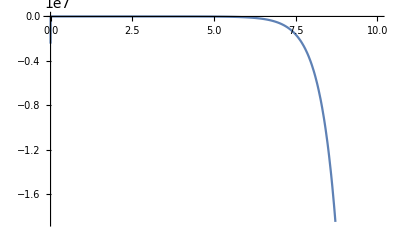

```mathematica
Plot[H^2 R[τ]^2 + μ/R[τ]^2/.R[τ]->Rsolnm[[2]]/.{C[1]->Log[μ]/(4 H)}/.{μ->1,H->1},{τ,0,10}]
```

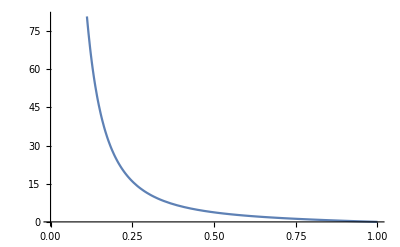

```mathematica
Plot[1/z^2 - z^2 ,{z,0,1}]
```

```mathematica
Rsoln[[2]]
```

(ⅇ^(-H (τ+C[1])) √(ⅇ^(4 H (τ+C[1]))-μ))/(√2 √H)

```mathematica
FullSimplify[Rsoln]
```

{-(ⅇ^(-H (τ+C[1])) √(ⅇ^(4 H (τ+C[1]))-μ))/(√2 √H),(ⅇ^(-H (τ+C[1])) √(ⅇ^(4 H (τ+C[1]))-μ))/(√2 √H)}

```mathematica
Solve[Rsoln==0,C[1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{C[1]→(-H τ+Log[-μ^(1/4)])/H},{C[1]→(-H τ+Log[-ⅈ μ^(1/4)])/H},{C[1]→(-H τ+Log[ⅈ μ^(1/4)])/H},{C[1]→(-4 H τ+Log[μ])/(4 H)}}

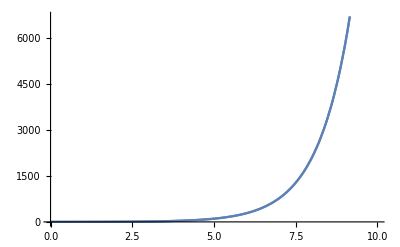

```mathematica
Show[Plot[(Rsoln[[2]])/.{C[1]->Log[μ]/(4 H)}/.{μ->1,H->1},{τ,0,10}],Plot[(Rsoln[[2]])/.{C[1]->Log[μ]/(4 H)}/.{μ->1,H->-1},{τ,0,10}]]
```

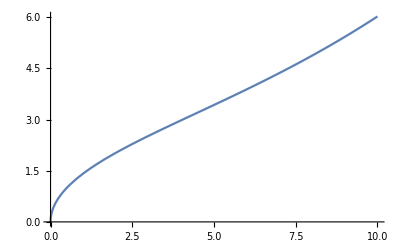

```mathematica
Plot[(Rsoln[[2]])/.{C[1]->Log[μ]/(4 H)}/.{μ->1,H->-0.1},{τ,0,10}]
```

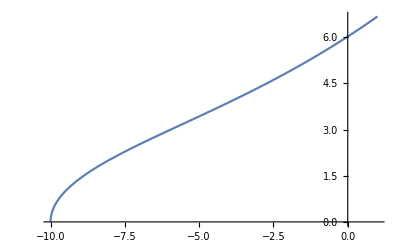

```mathematica
Plot[(Rsoln[[2]])/.{C[1]->Log[μ]/(4 H)+10}/.{μ->1,H->-0.1},{τ,-10,1}]
```

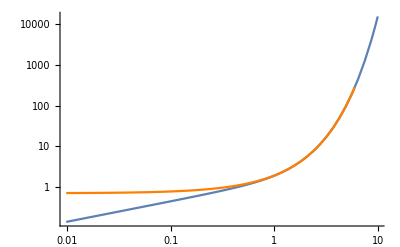

```mathematica
Show[LogLogPlot[Rsoln[[2]]/.{C[1]->Log[μ]/(4 H)}/.{μ->1,H->1},{τ,0,10}],LogLogPlot[Rsoln[[2]]/.{C[1]->0}/.{μ->0,H->1},{τ,0,10},PlotStyle->Orange]]
```

#### Anti desitter evolution

```mathematica
Rsoln=R[τ]/.DSolve[D[R[τ],τ]==(-H^2 R[τ]^2 + μ/R[τ]^2)^(1/2),R[τ],τ]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{-((-1)^(3/4) ⅇ^(-ⅈ H (τ+C[1])) √(ⅇ^(4 ⅈ H (τ+C[1]))-μ))/(√2 √H),((-1)^(3/4) ⅇ^(-ⅈ H (τ+C[1])) √(ⅇ^(4 ⅈ H (τ+C[1]))-μ))/(√2 √H)}

#### Jacobian test

```mathematica
x={z^2,y^2+w};
X = {z,y,w};
Table[D[x[[i]],X[[j]]],{i,2},{j,3}]
```

{{2 z,0,0},{0,2 y,1}}

```mathematica
x={√z,√(y-w)};
X = {z,y};
Table[D[x[[i]],X[[j]]],{i,2},{j,2}]
```

{{1/(2 √z),0},{0,1/(2 √(-w+y))}}

#### time component of Per Kraus

```mathematica
FullSimplify[((1-zh^4/z[τ]^4) + (z'[τ])^2)^(1/2)D[Log[1/z[τ]^2(1-zh^4/z[τ]^4)],τ]]
```

-(2 (-3 zh^4+z[τ]^4) z'[τ] √(1-zh^4/z[τ]^4+z'[τ]^2))/(-zh^4 z[τ]+z[τ]^5)

```mathematica
Simplify[D[((1-zh^4/z[τ]^4) + (z'[τ])^2)^(1/2),τ]]
```

(z'[τ] (2 zh^4+z[τ]^5 z''[τ]))/(z[τ]^5 √(1-zh^4/z[τ]^4+z'[τ]^2))

```mathematica
D[Log[1/z[τ]^2(1-zh^4/z[τ]^4)],τ]
```

(z[τ]^2 ((4 zh^4 z'[τ])/z[τ]^7-(2 (1-zh^4/z[τ]^4) z'[τ])/z[τ]^3))/(1-zh^4/z[τ]^4)

```mathematica
Simplify[D[(f[R[τ]]+R'[τ]^2)^(1/2)1/R[τ],τ]]
```

(R'[τ] (-2 f[R[τ]]-2 R'[τ]^2+R[τ] (f'[R[τ]]+2 R''[τ])))/(2 R[τ]^2 √(f[R[τ]]+R'[τ]^2))

Time  eqns

```mathematica
FullSimplify[((1-zp^4/z[τ]^4) + (z'[τ])^2)^(1/2)D[1/z[τ]^2(1-zp^4/z[τ]^4),z[τ]]]
FullSimplify[((1-zm^4/z[τ]^4) + (z'[τ])^2)^(1/2)D[1/z[τ]^2(1-zm^4/z[τ]^4),z[τ]]]
FullSimplify[%+%%]
```

-(2 (-3 zp^4+z[τ]^4) √(1-zp^4/z[τ]^4+z'[τ]^2))/z[τ]^7

-(2 (-3 zm^4+z[τ]^4) √(1-zm^4/z[τ]^4+z'[τ]^2))/z[τ]^7

(2 (-((-3 zm^4+z[τ]^4) √(1-zm^4/z[τ]^4+z'[τ]^2))-(-3 zp^4+z[τ]^4) √(1-zp^4/z[τ]^4+z'[τ]^2)))/z[τ]^7

time der of eqn

```mathematica
FullSimplify[D[((1-zp^4/z[τ]^4) + (z'[τ])^2)^(1/2)1/z[τ],τ]]
FullSimplify[D[((1-zm^4/z[τ]^4) + (z'[τ])^2)^(1/2)1/z[τ],τ]]
FullSimplify[%+%%]
```

-(z'[τ] (-3 zp^4+z[τ]^4 (1+z'[τ]^2-z[τ] z''[τ])))/(z[τ]^6 √(1-zp^4/z[τ]^4+z'[τ]^2))

-(z'[τ] (-3 zm^4+z[τ]^4 (1+z'[τ]^2-z[τ] z''[τ])))/(z[τ]^6 √(1-zm^4/z[τ]^4+z'[τ]^2))

(z'[τ] ((3 zm^4-z[τ]^4 (1+z'[τ]^2)+z[τ]^5 z''[τ])/(√(1-zm^4/z[τ]^4+z'[τ]^2))+(3 zp^4-z[τ]^4 (1+z'[τ]^2)+z[τ]^5 z''[τ])/(√(1-zp^4/z[τ]^4+z'[τ]^2))))/z[τ]^6

```mathematica
FullSimplify[D[((1-zm^4/z[τ]^4) + (z'[τ])^2)^(1/2)+((1-zp^4/z[τ]^4) + (z'[τ])^2)^(1/2),τ]]
```

z'[τ] (((2 zm^4)/z[τ]^5+z''[τ])/(√(1-zm^4/z[τ]^4+z'[τ]^2))+((2 zp^4)/z[τ]^5+z''[τ])/(√(1-zp^4/z[τ]^4+z'[τ]^2)))

Try squaring first

```mathematica
D[((1-zh^4/z[τ]^4) + (z'[τ])^2),τ]
```

(4 zh^4 z'[τ])/z[τ]^5+2 z'[τ] z''[τ]

```mathematica
Solve[((1-zh^4/z[τ]^4) + (z'[τ])^2)^(1/2)z''[τ]/z'[τ]^2 == σt,z''[τ]]
```

{{z''[τ]→(σt z'[τ]^2)/(√(1-zh^4/z[τ]^4+z'[τ]^2))}}

```mathematica
D[ ((1-zh^4/z[τ]^4) + (z'[τ])^2)^(1/2) ==  z[τ] σt,τ]
Simplify[Solve[%,z''[τ]]]
```

((4 zh^4 z'[τ])/z[τ]^5+2 z'[τ] z''[τ])/(2 √(1-zh^4/z[τ]^4+z'[τ]^2))==σt z'[τ]

{{z''[τ]→-(2 zh^4)/z[τ]^5+σt √(1-zh^4/z[τ]^4+z'[τ]^2)}}

```mathematica
D[ ((z[τ]^2-zh/z[τ]^2) + (z'[τ])^2)^(1/2) ==  z[τ] σt,τ]
Simplify[Solve[%,z''[τ]]]
```

((2 zh z'[τ])/z[τ]^3+2 z[τ] z'[τ]+2 z'[τ] z''[τ])/(2 √(-zh/z[τ]^2+z[τ]^2+z'[τ]^2))==σt z'[τ]

{{z''[τ]→-zh/z[τ]^3-z[τ]+σt √(-zh/z[τ]^2+z[τ]^2+z'[τ]^2)}}

```mathematica
Solve[((z[τ]^2-zh/z[τ]^2) + (z'[τ])^2)^(1/2)z''[τ]/z'[τ]^2 == σt,z''[τ]]
```

{{z''[τ]→(σt z'[τ]^2)/(√((-zh+z[τ]^4+z[τ]^2 z'[τ]^2)/z[τ]^2))}}

#### Check with Greater

```mathematica
Needs["Greater2`"]
```

Christoffel::shdw: Symbol Christoffel appears in multiple contexts {GREATER2`,Global`}; definitions in context GREATER2` may shadow or be shadowed by other definitions.

a::shdw: Symbol a appears in multiple contexts {GREATER2`,Global`}; definitions in context GREATER2` may shadow or be shadowed by other definitions.

b::shdw: Symbol b appears in multiple contexts {GREATER2`,Global`}; definitions in context GREATER2` may shadow or be shadowed by other definitions.

c::shdw: Symbol c appears in multiple contexts {GREATER2`,Global`}; definitions in context GREATER2` may shadow or be shadowed by other definitions.

l::shdw: Symbol l appears in multiple contexts {GREATER2`,Global`}; definitions in context GREATER2` may shadow or be shadowed by other definitions.

n::shdw: Symbol n appears in multiple contexts {GREATER2`,Global`}; definitions in context GREATER2` may shadow or be shadowed by other definitions.

ds2::shdw: Symbol ds2 appears in multiple contexts {GREATER2`,Global`}; definitions in context GREATER2` may shadow or be shadowed by other definitions.

dx::shdw: Symbol dx appears in multiple contexts {GREATER2`,Global`}; definitions in context GREATER2` may shadow or be shadowed by other definitions.

Metric::shdw: Symbol Metric appears in multiple contexts {GREATER2`,Global`}; definitions in context GREATER2` may shadow or be shadowed by other definitions.

Γ::shdw: Symbol Γ appears in multiple contexts {GREATER2`,Global`}; definitions in context GREATER2` may shadow or be shadowed by other definitions.

g::shdw: Symbol g appears in multiple contexts {GREATER2`,Global`}; definitions in context GREATER2` may shadow or be shadowed by other definitions.

Y::shdw: Symbol Y appears in multiple contexts {GREATER2`,Global`}; definitions in context GREATER2` may shadow or be shadowed by other definitions.

A::shdw: Symbol A appears in multiple contexts {GREATER2`,Global`}; definitions in context GREATER2` may shadow or be shadowed by other definitions.

λ::shdw: Symbol λ appears in multiple contexts {GREATER2`,Global`}; definitions in context GREATER2` may shadow or be shadowed by other definitions.

t$::shdw: Symbol t$ appears in multiple contexts {GREATER2`,Global`}; definitions in context GREATER2` may shadow or be shadowed by other definitions.

y$::shdw: Symbol y$ appears in multiple contexts {GREATER2`,Global`}; definitions in context GREATER2` may shadow or be shadowed by other definitions.

GREATER has been loaded. Some functions = antisymmetrize, CoD (covariant derivative), Contract, ds2met (covert line element to metric), Epsilon, KillingEquations, SimpleDeriv (partial derivative), LieD (Lie derivative), ChangeCoords, DAlembertian , FieldStrength (F = dA), IndexShift, symmetrize, TJacobian, Trans2rules, SelfContract, CottonTensor, wedge, ExtrinsicCurvature, ShowComponents

Needs::nocont: Context Greater2` was not created when Needs was evaluated.

```mathematica
Clear[t,w,x]
X = {t,x,y,w,z}
(*Y = {t,x,w,z}*)
Y = {t,x,y, w}
diffs4D= {dt,dx,dy,dw}

met4D = diffs4D.DiagonalMatrix[{-(1-z^4/zh^4),1,1,1}].diffs4D (*should check that this also holds for general metrics. Though not sure how to do it here. There is likley an analytic way to do it*)


ds2 = L^2 / z^2 (met4D+dz^2/(1-z^4/zh^4))

GDD = Metric[ds2,X]
```

{t,x,y,w,z}

{t,x,y,w}

{dt,dx,dy,dw}

dw^2+dx^2+dy^2+dt^2 (-1+z^4/zh^4)

(L^2 (dw^2+dx^2+dy^2+dz^2/(1-z^4/zh^4)+dt^2 (-1+z^4/zh^4)))/z^2

{{(L^2 (-1+z^4/zh^4))/z^2,0,0,0,0},{0,L^2/z^2,0,0,0},{0,0,L^2/z^2,0,0},{0,0,0,L^2/z^2,0},{0,0,0,0,L^2/(z^2 (1-z^4/zh^4))}}

```mathematica
Clear[u,n]
f[z_]:=(1-z^4/zh^4)
```

```mathematica
u = {(z^2/L^2 f[z] + zd^2)^(1/2)1/f[z],0,0,0,zd};
n = {-zd/f[z],0,0,0,-(z^2/L^2 f[z] + zd^2)^(1/2)};
Γ = Christoffel[GDD,X]; (* first is up, other two are down*)
Knon=Simplify[n.GDD.Γ]
```

{{(L^2 √(zd^2+(z^2-z^6/zh^4)/L^2) (z^4+zh^4))/(z^3 zh^4),0,0,0,(L^2 zd (z^4+zh^4))/(z^7-z^3 zh^4)},{0,-(L^2 √(zd^2+(z^2-z^6/zh^4)/L^2))/z^3,0,0,0},{0,0,-(L^2 √(zd^2+(z^2-z^6/zh^4)/L^2))/z^3,0,0},{0,0,0,-(L^2 √(zd^2+(z^2-z^6/zh^4)/L^2))/z^3,0},{(L^2 zd (z^4+zh^4))/(z^7-z^3 zh^4),0,0,0,(L^2 √(zd^2+(z^2-z^6/zh^4)/L^2) zh^4 (-3 z^4+zh^4))/(z^3 (z^4-zh^4)^2)}}

```mathematica
Simplify[D[GDD[[5,5]],z]]
```

-(2 L^2 zh^4 (-3 z^4+zh^4))/(z^3 (z^4-zh^4)^2)

```mathematica
FullSimplify[u.GDD.u]
FullSimplify[n.GDD.n]
```

-1

1

```mathematica
Clear[zd,dtz]
FullSimplify[Table[u.Table[D[X[[j]]/.{t->t0[t,z],x->0,y->0,w->0,z->z0[t,z]},X[[i]]],{i,5}] + (u.Γ[[j,;;,;;]].(X/.z->z0[t,z])),{j,5}]]/.{D[z0[t,z],z]->1,D[t0[t,z],t]->1,x->0,y->0,w->0}
Simplify[JXxPL.%]
Table[D[XPL[[j]],X[[i]]],{i,5},{j,5}]
JXxPL
(*dtz = dtz/.FullSimplify[Solve[zd==%,dtz]];
Limit[dtz,z0[t,z]->zh];*)
```

{(-√(zd^2+(z^2-z^6/zh^4)/L^2) zh^4 (z^4+zh^4) z0[t,z]+(z^4-zh^4) (-z √(zd^2+(z^2-z^6/zh^4)/L^2) zh^4+t zd (z^4+zh^4)+z zd (z^4-zh^4) t0^(0,1)[t,z]))/(z (z^4-zh^4)^2),0,0,0,zd+(zd (-3 z^4+zh^4) z0[t,z])/(z^5-z zh^4)-(√(zd^2+(z^2-z^6/zh^4)/L^2) (t (z^8-zh^8)+z zh^8 z0^(1,0)[t,z]))/(zh^4 (z^5-z zh^4))}

{1/(z (z^4-zh^4)^2)(-√(zd^2+(z^2-z^6/zh^4)/L^2) zh^4 (z^4+zh^4) z0[t,z]+(z^4-zh^4) (-z √(zd^2+(z^2-z^6/zh^4)/L^2) zh^4+t zd (z^4+zh^4)+z zd (z^4-zh^4) t0^(0,1)[t,z])+(z^7 (z^4-zh^4) (zd+(zd (-3 z^4+zh^4) z0[t,z])/(z^5-z zh^4)-(√(zd^2+(z^2-z^6/zh^4)/L^2) (t (z^8-zh^8)+z zh^8 z0^(1,0)[t,z]))/(zh^4 (z^5-z zh^4))))/zh^2),0,0,0,zd+(zd (-3 z^4+zh^4) z0[t,z])/(z^5-z zh^4)-(√(zd^2+(z^2-z^6/zh^4)/L^2) (t (z^8-zh^8)+z zh^8 z0^(1,0)[t,z]))/(zh^4 (z^5-z zh^4))}

{{1,0,0,0,0},{0,0,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{1/(2 (1+z^2/zh^2))+z^2/zh^2-zh/(4 (-z+zh))-zh/(4 (z+zh)),0,0,0,1}}

{{1,0,0,0,z^6/(z^4 zh^2-zh^6)},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}

```mathematica
Clear[zd,dtz]
Simplify[u.Table[D[z0[t,z],X[[i]]],{i,5}] + (u.Γ[[5,;;,;;]].X)]/.{D[z0[t,z],z]->1,D[z0[t,z],t]->dtz,z->z0[t,z]}
% + u[[5]] z^2/(zh^2 f[z]) dtz
dtz = dtz/.FullSimplify[Solve[zd==%,dtz]]
Limit[dtz,z0[t,z]->zh]
```

zd+(zd (zh^4-3 z0[t,z]^4))/(-zh^4+z0[t,z]^4)-(t (zh^4+z0[t,z]^4) √(zd^2+(z0[t,z]^2-z0[t,z]^6/zh^4)/L^2))/(zh^4 z0[t,z])+(dtz √(zd^2+(z0[t,z]^2-z0[t,z]^6/zh^4)/L^2))/(1-z0[t,z]^4/zh^4)

zd+(dtz z^2 zd)/(zh^2 (1-zh^4/z^4))+(zd (zh^4-3 z0[t,z]^4))/(-zh^4+z0[t,z]^4)-(t (zh^4+z0[t,z]^4) √(zd^2+(z0[t,z]^2-z0[t,z]^6/zh^4)/L^2))/(zh^4 z0[t,z])+(dtz √(zd^2+(z0[t,z]^2-z0[t,z]^6/zh^4)/L^2))/(1-z0[t,z]^4/zh^4)

{((zd (zh^4-3 z0[t,z]^4))/(-zh^4+z0[t,z]^4)-(t (zh^4+z0[t,z]^4) √(zd^2+(z0[t,z]^2-z0[t,z]^6/zh^4)/L^2))/(zh^4 z0[t,z]))/((z^6 zd)/(-z^4 zh^2+zh^6)-(√(zd^2+(z0[t,z]^2-z0[t,z]^6/zh^4)/L^2))/(1-z0[t,z]^4/zh^4))}

{-(2 zd)/(√(zd^2))}

```mathematica
Clear[zd,dtz]
u.Table[D[z0[t],X[[i]]],{i,5}] 
(u.Γ[[5,;;,;;]].X)
u[[5]]Γ[[5,5,5]] X[[5]]
u.Table[D[z0[t],X[[i]]],{i,5}] + (u.Γ[[5,;;,;;]].X)/.{D[z0[t],z]->1,D[z0[t],t]->dtz,z->z0[t]}
dtz = dtz/.FullSimplify[Solve[zd==%,dtz]]
Limit[dtz,z0[t]->zh]
```

(√(zd^2+(z^2 (1-z^4/zh^4))/L^2) z0'[t])/(1-z^4/zh^4)

(t √(zd^2+(z^2 (1-z^4/zh^4))/L^2) (-1/z+z^7/zh^8))/(1-z^4/zh^4)+(z zd (-3 z^4+zh^4))/(z^5-z zh^4)

(z zd (-3 z^4+zh^4))/(z^5-z zh^4)

(zd z0[t] (zh^4-3 z0[t]^4))/(-zh^4 z0[t]+z0[t]^5)+(dtz √(zd^2+(z0[t]^2 (1-z0[t]^4/zh^4))/L^2))/(1-z0[t]^4/zh^4)+(t (-1/z0[t]+z0[t]^7/zh^8) √(zd^2+(z0[t]^2 (1-z0[t]^4/zh^4))/L^2))/(1-z0[t]^4/zh^4)

{(2 zd zh^8 z0[t]-4 zd zh^4 z0[t]^5+t zh^8 √(zd^2+(z0[t]^2 (1-z0[t]^4/zh^4))/L^2)-t z0[t]^8 √(zd^2+(z0[t]^2 (1-z0[t]^4/zh^4))/L^2))/(zh^8 z0[t] √(zd^2+(z0[t]^2 (1-z0[t]^4/zh^4))/L^2))}

{-(2 zd)/(√(zd^2))}

```mathematica
Clear[x,Y]
f[z_]:=1 - zh^4/z^4
met5D = l^2/z^2{{-f[z],0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1/f[z]}}
Y= {t,x,y,w,z};

(*Painleve*)
XPL= {t+ Integrate[z^2/(zh^2 f[z]),z],x,y,w,z};
JXxPL=FullSimplify[Table[D[XPL[[i]],Y[[j]]],{i,5},{j,5}]]
gPL = FullSimplify[Transpose[JXxPL].met5D.JXxPL]
FullSimplify[Inverse[JXxPL]];

ΓPL = FullSimplify[Christoffel[gPL,Y]];
%[[5]]
```

{{(l^2 (-1+zh^4/z^4))/z^2,0,0,0,0},{0,l^2/z^2,0,0,0},{0,0,l^2/z^2,0,0},{0,0,0,l^2/z^2,0},{0,0,0,0,l^2/(z^2 (1-zh^4/z^4))}}

{{1,0,0,0,z^6/(z^4 zh^2-zh^6)},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}

{{(l^2 (-z^4+zh^4))/z^6,0,0,0,-l^2/zh^2},{0,l^2/z^2,0,0,0},{0,0,l^2/z^2,0,0},{0,0,0,l^2/z^2,0},{-l^2/zh^2,0,0,0,-(l^2 z^2)/zh^4}}

{{-(z^8-4 z^4 zh^4+3 zh^8)/z^9,0,0,0,-z/zh^2+(3 zh^2)/z^3},{0,(z^4-zh^4)/z^5,0,0,0},{0,0,(z^4-zh^4)/z^5,0,0},{0,0,0,(z^4-zh^4)/z^5,0},{-z/zh^2+(3 zh^2)/z^3,0,0,0,1/z-z^3/zh^4}}

```mathematica
uPL = {uPLt,0,0,0,dz}
FullSimplify[Solve[-1==uPL.gPL.uPL,uPLt]]
nPL = {nPLt,0,0,0,nPLz}
Simplify[Solve[{1==nPL.gPL.nPL,0==nPL.gPL.uPL},{nPLt,nPLz}]]
```

{uPLt,0,0,0,dz}

{{uPLt→(z^3 (dz l^2 z^3-zh^2 √(l^2 (dz^2 l^2 z^2+z^4-zh^4))))/(l^2 zh^2 (-z^4+zh^4))},{uPLt→(z^3 (dz l^2 z^3+zh^2 √(l^2 (dz^2 l^2 z^2+z^4-zh^4))))/(l^2 zh^2 (-z^4+zh^4))}}

{nPLt,0,0,0,nPLz}

{{nPLt→-(ⅈ z^5 (dz z^2+uPLt zh^2))/(√(-l^2 zh^4 (dz^2 z^8+2 dz uPLt z^6 zh^2+uPLt^2 zh^4 (z^4-zh^4)))),nPLz→(ⅈ (dz z^6 zh^2+uPLt zh^4 (z^4-zh^4)))/(z √(-l^2 zh^4 (dz^2 z^8+2 dz uPLt z^6 zh^2+uPLt^2 zh^4 (z^4-zh^4))))},{nPLt→(ⅈ z^5 (dz z^2+uPLt zh^2))/(√(-l^2 zh^4 (dz^2 z^8+2 dz uPLt z^6 zh^2+uPLt^2 zh^4 (z^4-zh^4)))),nPLz→-(ⅈ (dz z^6 zh^2+uPLt zh^4 (z^4-zh^4)))/(z √(-l^2 zh^4 (dz^2 z^8+2 dz uPLt z^6 zh^2+uPLt^2 zh^4 (z^4-zh^4))))}}

```mathematica
ΓPL[[5,5,5]]
```

1/z-z^3/zh^4

```mathematica
PowerExpand[A 1/zh==A (ρM/A)^(3/4)]
```

A/zh==A^(1/4) ρM^(3/4)

```mathematica
Series[1 - (1- x)^(3/4),{x,0,1}]
```

(3 x)/4+O[x]^2

```mathematica
Clear[zd,dtz]
Simplify[u.Table[D[z0[t,z],X[[i]]],{i,5}] + (u.ΓPL[[5,;;,;;]].X)]/.{D[z0[t,z],z]->1,D[z0[t,z],t]->dtz,z->z0[t,z]}
dtz = dtz/.FullSimplify[Solve[zd==%,dtz]]
Limit[dtz,z0[t,z]->zh]
```

2 zd-(zd z0[t,z]^4)/zh^4+t zd ((3 zh^2)/z0[t,z]^3-z0[t,z]/zh^2)-(t zh^4 (3 zh^4-z0[t,z]^4) √(zd^2+(z0[t,z]^2-z0[t,z]^6/zh^4)/L^2))/z0[t,z]^9+(dtz √(zd^2+(z0[t,z]^2-z0[t,z]^6/zh^4)/L^2))/(1-z0[t,z]^4/zh^4)-(zh^2 (3 zh^4-z0[t,z]^4) √(zd^2+(z0[t,z]^2-z0[t,z]^6/zh^4)/L^2))/(-zh^4 z0[t,z]^2+z0[t,z]^6)

{-((1-z0[t,z]^4/zh^4) (zd-(zd z0[t,z]^4)/zh^4+t zd ((3 zh^2)/z0[t,z]^3-z0[t,z]/zh^2)+(zh^2 (3 zh^4-z0[t,z]^4) √(zd^2+(z0[t,z]^2-z0[t,z]^6/zh^4)/L^2))/(z0[t,z]^2 (zh^4-z0[t,z]^4))+(t zh^4 (-3 zh^4+z0[t,z]^4) √(zd^2+(z0[t,z]^2-z0[t,z]^6/zh^4)/L^2))/z0[t,z]^9))/(√(zd^2+(z0[t,z]^2-z0[t,z]^6/zh^4)/L^2))}

{-2}

```mathematica
Clear[zd,dtz]
Simplify[u.Table[D[z0[t,z],X[[i]]],{i,5}] + (u.Γ[[5,;;,;;]].X)]/.{D[z0[t,z],z]->1,D[z0[t,z],t]->dtz,z->z0[t,z]}
dtz = dtz/.FullSimplify[Solve[zd==%,dtz]]
Limit[dtz,z0[t,z]->zh]
```

D::dvar: Multiple derivative specifier {t,v,y,w,z} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

Dot::rect: Nonrectangular tensor encountered.

zd+{-((zh^4+z0[t,z]^4) √(zd^2+(z0[t,z]^2-z0[t,z]^6/zh^4)/L^2))/(zh^4 z0[t,z]),0,0,0,(zd (zh^4-3 z0[t,z]^4))/(-zh^4 z0[t,z]+z0[t,z]^5)}.{t,{t,v,y,w,z0[t,z]},y,w,z0[t,z]}+(dtz √(zd^2+(z0[t,z]^2-z0[t,z]^6/zh^4)/L^2))/(1-z0[t,z]^4/zh^4)

{({-((zh^4+z0[t,z]^4) √(zd^2+(z0[t,z]^2-z0[t,z]^6/zh^4)/L^2))/(zh^4 z0[t,z]),0,0,0,(zd (zh^4-3 z0[t,z]^4))/(-zh^4 z0[t,z]+z0[t,z]^5)}.{t,{t,v,y,w,z0[t,z]},y,w,z0[t,z]} (-zh^4+z0[t,z]^4))/(zh^4 √(zd^2+(z0[t,z]^2-z0[t,z]^6/zh^4)/L^2))}

$Aborted

```mathematica
Clear[zd,dtz]
u.Table[D[z0[t],X[[i]]],{i,5}] 
(u.Γ[[5,;;,;;]].X)
u.Table[D[z0[t],X[[i]]],{i,5}] + (u.Γ[[5,;;,;;]].X)/.{D[z0[t],z]->1,D[z0[t],t]->dtz,z->z0[t]}
dtz = dtz/.FullSimplify[Solve[zd==%,dtz]]
Limit[dtz,z0[t]->zh]
```

```mathematica
JXxPL[[5]]
```

{0,0,0,0,1}

```mathematica
Clear[zd,dtt,dzt]
Simplify[u.Table[D[t0[t,z],X[[i]]],{i,5}] + (u.Γ[[1,;;,;;]].X)]/.{D[t0[t,z],z]->dzt,D[t0[t,z],t]->1,t->t0[t,z]}
dzt = dzt/.FullSimplify[Solve[u[[1]]==%,dzt]]
Limit[dzt,z->zh]
```

dzt zd+(√(zd^2+(z^2-z^6/zh^4)/L^2) zh^4)/(-z^4+zh^4)+((z^4+zh^4) (-z √(zd^2+(z^2-z^6/zh^4)/L^2) zh^4+zd (z^4-zh^4) t0[t,z]))/(z (z^4-zh^4)^2)

{((z^4+zh^4) (z √(zd^2+(z^2-z^6/zh^4)/L^2) zh^4+zd (-z^4+zh^4) t0[t,z]))/(z zd (z^4-zh^4)^2)}

$Aborted

```mathematica
FullSimplify[Γ[[5,;;,;;]]]
FullSimplify[Γ[[1,;;,;;]]]
```

{{-1/z+z^7/zh^8,0,0,0,0},{0,1/z-z^3/zh^4,0,0,0},{0,0,1/z-z^3/zh^4,0,0},{0,0,0,1/z-z^3/zh^4,0},{0,0,0,0,(-3 z^4+zh^4)/(z^5-z zh^4)}}

{{0,0,0,0,(z^4+zh^4)/(z^5-z zh^4)},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{(z^4+zh^4)/(z^5-z zh^4),0,0,0,0}}

```mathematica
GDD[[1,1]]
Simplify[D[GDD[[1,1]],z]]
%n[[5]]
```

-(L^2 (z^4-zh^4))/z^6

(2 L^2 (z^4-3 zh^4))/z^7

-(2 L^4 (z^4-3 zh^4) √(zd^2+(z^2 (1-zh^4/z^4))/L^2))/z^9

```mathematica
Simplify[n.GDD/.{z->z[t],zd->z'[t]}]
Simplify[D[%,t]]
FullSimplify[(Knon[[1,1]] /.{z->z[t],zd->z'[t]})+ %[[1]]]
```

{(L^4 z'[t])/z[t]^4,0,0,0,-(L^4 √((-zh^4+z[t]^4)/(L^2 z[t]^2)+z'[t]^2))/(-zh^4+z[t]^4)}

{(L^4 (-4 z'[t]^2+z[t] z''[t]))/z[t]^5,0,0,0,(L^2 z'[t] (zh^8-4 zh^4 z[t]^4+3 z[t]^8+4 L^2 z[t]^6 z'[t]^2+L^2 zh^4 z[t]^3 z''[t]-L^2 z[t]^7 z''[t]))/(z[t]^3 (zh^4-z[t]^4)^2 √(-zh^4/(L^2 z[t]^2)+z[t]^2/L^2+z'[t]^2))}

(L^4 (-3 zh^4+z[t]^4) √((-zh^4+z[t]^4)/(L^2 z[t]^2)+z'[t]^2))/z[t]^9+(L^4 (-4 z'[t]^2+z[t] z''[t]))/z[t]^5

```mathematica
Information[Christoffel]
```

```mathematica
Simplify[D[K[[2,2]]/GDD[[2,2]]/.{z->z[t],zd->z'[t]},t]]
```

(z'[t] (-4 zh^4+2 z[t]^4+3 L^2 z[t]^2 z'[t]^2-L^2 z[t]^3 z''[t]))/(z[t]^6 √(-zh^4/(L^2 z[t]^2)+z[t]^2/L^2+z'[t]^2))

```mathematica
Simplify[n.GDD/.{z->z[t],zd->z'[t]}]
parn = FullSimplify[Table[D[%[[i]],X[[j]]/.z->z[t]],{i,5},{j,5}]] (*partial derivative of n*)
K4DD = (Knon + %)[[1;;4,1;;4]] /.{z->z[t],zd->z'[t]}
```

{(L^4 z'[t])/z[t]^4,0,0,0,-(L^4 √((-zh^4+z[t]^4)/(L^2 z[t]^2)+z'[t]^2))/(-zh^4+z[t]^4)}

{{(L^4 (-4 z'[t]^2+z[t] z''[t]))/z[t]^5,0,0,0,-(4 L^4 z'[t])/z[t]^5},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{(L^2 z'[t] (zh^8-4 zh^4 z[t]^4+3 z[t]^8+4 L^2 z[t]^6 z'[t]^2+L^2 z[t]^3 (zh^4-z[t]^4) z''[t]))/(z[t]^3 (zh^4-z[t]^4)^2 √((-zh^4+z[t]^4)/(L^2 z[t]^2)+z'[t]^2)),0,0,0,(L^2 (zh^8-4 zh^4 z[t]^4+3 z[t]^8+4 L^2 z[t]^6 z'[t]^2))/(z[t]^3 (zh^4-z[t]^4)^2 √((-zh^4+z[t]^4)/(L^2 z[t]^2)+z'[t]^2))}}

{{(L^4 (-3 zh^4+z[t]^4) √((-zh^4+z[t]^4)/(L^2 z[t]^2)+z'[t]^2))/z[t]^9+(L^4 (-4 (z[t]'[t])^2+z[t][t] z[t]''[t]))/(z[t][t])^5,0,0,0},{0,-(L^4 √((-zh^4+z[t]^4)/(L^2 z[t]^2)+z'[t]^2))/z[t]^5,0,0},{0,0,-(L^4 √((-zh^4+z[t]^4)/(L^2 z[t]^2)+z'[t]^2))/z[t]^5,0},{0,0,0,-(L^4 √((-zh^4+z[t]^4)/(L^2 z[t]^2)+z'[t]^2))/z[t]^5}}

```mathematica
u4=u[[1;;4]]
GUU = Inverse[GDD]
GUU4 = %[[1;;4,1;;4]]
Simplify[Sum[(GUU4.K4DD)[[i,i]],{i,4}]]
```

{(√(zd^2+(z^2 (1-zh^4/z^4))/L^2))/(1-zh^4/z^4),0,0,0}

{{L^8/(z^4 (z^4-zh^4) (-L^10/(z^6 (z^4-zh^4))+(L^10 zh^4)/(z^10 (z^4-zh^4)))),0,0,0,0},{0,(-L^8/(z^4 (z^4-zh^4))+(L^8 zh^4)/(z^8 (z^4-zh^4)))/(-L^10/(z^6 (z^4-zh^4))+(L^10 zh^4)/(z^10 (z^4-zh^4))),0,0,0},{0,0,(-L^8/(z^4 (z^4-zh^4))+(L^8 zh^4)/(z^8 (z^4-zh^4)))/(-L^10/(z^6 (z^4-zh^4))+(L^10 zh^4)/(z^10 (z^4-zh^4))),0,0},{0,0,0,(-L^8/(z^4 (z^4-zh^4))+(L^8 zh^4)/(z^8 (z^4-zh^4)))/(-L^10/(z^6 (z^4-zh^4))+(L^10 zh^4)/(z^10 (z^4-zh^4))),0},{0,0,0,0,(-L^8/z^8+(L^8 zh^4)/z^12)/(-L^10/(z^6 (z^4-zh^4))+(L^10 zh^4)/(z^10 (z^4-zh^4)))}}

{{L^8/(z^4 (z^4-zh^4) (-L^10/(z^6 (z^4-zh^4))+(L^10 zh^4)/(z^10 (z^4-zh^4)))),0,0,0},{0,(-L^8/(z^4 (z^4-zh^4))+(L^8 zh^4)/(z^8 (z^4-zh^4)))/(-L^10/(z^6 (z^4-zh^4))+(L^10 zh^4)/(z^10 (z^4-zh^4))),0,0},{0,0,(-L^8/(z^4 (z^4-zh^4))+(L^8 zh^4)/(z^8 (z^4-zh^4)))/(-L^10/(z^6 (z^4-zh^4))+(L^10 zh^4)/(z^10 (z^4-zh^4))),0},{0,0,0,(-L^8/(z^4 (z^4-zh^4))+(L^8 zh^4)/(z^8 (z^4-zh^4)))/(-L^10/(z^6 (z^4-zh^4))+(L^10 zh^4)/(z^10 (z^4-zh^4)))}}

(L^2 z^2 ((3 z^4 zh^4+(-4 z^4+3 zh^4) z[t]^4) (z[t][t])^5 √(-zh^4/(L^2 z[t]^2)+z[t]^2/L^2+z'[t]^2)+4 z^4 z[t]^9 (z[t]'[t])^2-z^4 z[t]^9 z[t][t] z[t]''[t]))/((z^4-zh^4) z[t]^9 (z[t][t])^5)

#### Wilczek tunneling pole studies

```mathematica
zd^2 + f[z] - (z^3 (a+ b n[[5]]))^2
```

1+zd^2-zh^4/z^4-z^6 (a-(b L^2 √(zd^2+(z^2 (1-zh^4/z^4))/L^2))/z^2)^2

```mathematica
Solve[zd^2 + f[z] - (z^3 (a+ b n[[5]]))^2==0/.b->0,zd]
```

{{zd→-(√(-z^4+a^2 z^10+zh^4))/z^2},{zd→(√(-z^4+a^2 z^10+zh^4))/z^2}}

```mathematica
Solve[zt^2-zh^4 == zt^5 a,zt]
```

{{zt→Root[zh^4-#1^2+a #1^5&,1]},{zt→Root[zh^4-#1^2+a #1^5&,2]},{zt→Root[zh^4-#1^2+a #1^5&,3]},{zt→Root[zh^4-#1^2+a #1^5&,4]},{zt→Root[zh^4-#1^2+a #1^5&,5]}}

Assume small correction to zh from presence of potential. So only really valid for a away from zh^6

```mathematica
Series[1- zh^4/z^4 - z^6 a /.z->zh+ϵ,{ϵ,0,1}]
Solve[Normal[%]==0,ϵ]
FullSimplify[zh + ϵ /.%[[1]]]
```

-a zh^6+(4/zh-6 a zh^5) ϵ+O[ϵ]^2

{{ϵ→-(a zh^7)/(2 (-2+3 a zh^6))}}

zh+(a zh^7)/(4-6 a zh^6)

```mathematica
Series[√z,{z,0,10}]
```

√z+O[z]^(21/2)

```mathematica
Solve[-z^4+ a z^2-b==0,z]
z0 =z/.%[[2]]/.{a->2,b->1}
```

{{z→-(√(a-√(a^2-4 b)))/(√2)},{z→(√(a-√(a^2-4 b)))/(√2)},{z→-(√(a+√(a^2-4 b)))/(√2)},{z→(√(a+√(a^2-4 b)))/(√2)}}

1

```mathematica
(1/(√(a-z^2-b 1/z^2))/.{a->2,b->1,z->z0-ϵ})
Series[%,{ϵ,z0,1}]
PowerExpand[%]
```

1/(√(2-1/(1-ϵ)^2-(1-ϵ)^2))

(ϵ-1)/(√(-1/(-1+ϵ)^2) (-1+ϵ))+O[ϵ-1]^2

-ⅈ (ϵ-1)+O[ϵ-1]^2

```mathematica
N[√5]
```

2.23607

```mathematica
a z^2-b/z^2
Solve[%==0,z]
z0 =z/.%[[4]]/.{a->1,b->1}
(1/(√(a z^2-b/z^2))/.{a->1,b->1,z->z0+ϵ})
Series[%,{ϵ,0,1}]
PowerExpand[%]
```

-b/z^2+a z^2

{{z→-b^(1/4)/a^(1/4)},{z→-(ⅈ b^(1/4))/a^(1/4)},{z→(ⅈ b^(1/4))/a^(1/4)},{z→b^(1/4)/a^(1/4)}}

1

1/(√(-1/(1+ϵ)^2+(1+ϵ)^2))

1/(2 √ϵ)+(√ϵ)/8+O[ϵ]^(3/2)

1/(2 √ϵ)+(√ϵ)/8+O[ϵ]^(3/2)

```mathematica
Normal[1/(2 √ϵ)+(√ϵ)/8+O[ϵ]^(3/2)]
```

1/(2 √ϵ)+(√ϵ)/8

```mathematica
Series[1/(√(1-1/z^2)),{1/z,1,1}]
```

1/(√2 √(z-1))+(3 √(z-1))/(4 √2)+O[z-1]^(3/2)

#### Diff zh energy

```mathematica
FullSimplify[Solve[√((1-zhp^4/z^4) + zds)+√((1-zhm^4/z^4) + zds)== z/L σ/σc,zds]]
FullSimplify[Solve[√(fp + zds)+√(fm + zds)== z/L σ/σc,zds]]
FullSimplify[% /. fm->fp]
FullSimplify[%%% /. zhm->zhp]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{zds→1/4 (-4+(2 (zhm^4+zhp^4))/z^4+(z^2 σ^2)/(L^2 σc^2)+(L^2 (zhm^4-zhp^4)^2 σc^2)/(z^10 σ^2))}}

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{zds→1/4 (-2 (fm+fp)+(z^2 σ^2)/(L^2 σc^2)+((fm-fp)^2 L^2 σc^2)/(z^2 σ^2))}}

{{zds→-fp+(z^2 σ^2)/(4 L^2 σc^2)}}

{{zds→-1+zhp^4/z^4+(z^2 σ^2)/(4 L^2 σc^2)}}

```mathematica
FullSimplify[Solve[√(fp + zds)+√(fm + zds)== z^3/L^3 (ρ + ϕs )/σc,zds]]
```

```mathematica
Integrate[1/(√(b-a x)),x]
(%/.x->ρω) -(%/.x->0)
```

-(2 √(b-a x))/a

(2 √b)/a-(2 √(b-a ρω))/a

```mathematica
Integrate[1/(1-√((2 (M - ω))/r)),r]
Integrate[%,ω]
```

r+2 √2 r √((M-ω)/r)+4 (M-ω) Log[-1+√2 √((M-ω)/r)]-2 (M-ω) Log[(M-ω)/r]

-4/3 √2 r (M-ω) √((M-ω)/r)+M ω+r ω-ω^2/2-4 r^2 (-(M-ω)^2/(8 r^2)-(√((M-ω)/r))/(4 √2)-((M-ω)/r)^(3/2)/(6 √2)+ω/(8 r)-1/8 Log[1-√2 √((M-ω)/r)])-2 (M-ω)^2 Log[-1+√2 √((M-ω)/r)]+(M-ω)^2 Log[(M-ω)/r]

```mathematica
D[√r]
```

#### Solve for z eom

```mathematica
FullSimplify[Solve[√(z^2/l^2(1-zhp^4/z^4) + zds)+√(z^2/l^2(1-zhm^4/z^4) + zds)== z/l (2 σ)/σc,zds]]
FullSimplify[Solve[√(z^2/l^2 fp + zds)+√(z^2/l^2 fm + zds)== z/l (2 σ)/σc,zds]]
FullSimplify[% /. fm->fp]
Simplify[%%% ]
Simplify[% /.zhm->zhp]
(*/.σ->σc √((H l)^2 +1)*)
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{zds→(16 z^8 σ^4+8 z^4 (-2 z^4+zhm^4+zhp^4) σ^2 σc^2+(zhm^4-zhp^4)^2 σc^4)/(16 l^2 z^6 σ^2 σc^2)}}

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{zds→(z^2 (16 σ^4-8 (fm+fp) σ^2 σc^2+(fm-fp)^2 σc^4))/(16 l^2 σ^2 σc^2)}}

{{zds→(z^2 (σ^2-fp σc^2))/(l^2 σc^2)}}

{{zds→(16 z^8 σ^4+8 z^4 (-2 z^4+zhm^4+zhp^4) σ^2 σc^2+(zhm^4-zhp^4)^2 σc^4)/(16 l^2 z^6 σ^2 σc^2)}}

{{zds→(zhp^4 σc^2+z^4 (σ^2-σc^2))/(l^2 z^2 σc^2)}}

```mathematica
FullSimplify[Solve[√(z^2/l^2(1-z^4/zhp^4) + zds)+√(z^2/l^2(1-z^4/zhm^4) + zds)== z/l (2 σ)/σc,zds]]
zd =FullSimplify[Solve[√(z^2/l^2 fp + zds)+√(z^2/l^2 fm + zds)== z/l (2 σ)/σc,zds]]
FullSimplify[% /. fm->fp]
FullSimplify[%%% ]
Simplify[% /.zhm->zhp]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{zds→(z^2 (16 zhm^8 zhp^8 σ^4+8 zhm^4 zhp^4 (-2 zhm^4 zhp^4+z^4 (zhm^4+zhp^4)) σ^2 σc^2+z^8 (zhm^4-zhp^4)^2 σc^4))/(16 l^2 zhm^8 zhp^8 σ^2 σc^2)}}

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{zds→(z^2 (16 σ^4-8 (fm+fp) σ^2 σc^2+(fm-fp)^2 σc^4))/(16 l^2 σ^2 σc^2)}}

{{zds→(z^2 (σ^2-fp σc^2))/(l^2 σc^2)}}

{{zds→(z^2 (16 zhm^8 zhp^8 σ^4+8 zhm^4 zhp^4 (-2 zhm^4 zhp^4+z^4 (zhm^4+zhp^4)) σ^2 σc^2+z^8 (zhm^4-zhp^4)^2 σc^4))/(16 l^2 zhm^8 zhp^8 σ^2 σc^2)}}

{{zds→(z^2 (-1+z^4/zhp^4+σ^2/σc^2))/l^2}}

```mathematica
Solve[a z^6 + b z^2 + c z^10 ==0,z ]
Solve[(a z^6 + b z^2 + c z^10 /.c->0)==0,z ]
```

{{z→0},{z→0},{z→-((-a/c-(√(a^2-4 b c))/c)^(1/4))/2^(1/4)},{z→-(ⅈ (-a/c-(√(a^2-4 b c))/c)^(1/4))/2^(1/4)},{z→(ⅈ (-a/c-(√(a^2-4 b c))/c)^(1/4))/2^(1/4)},{z→((-a/c-(√(a^2-4 b c))/c)^(1/4))/2^(1/4)},{z→-((-a/c+(√(a^2-4 b c))/c)^(1/4))/2^(1/4)},{z→-(ⅈ (-a/c+(√(a^2-4 b c))/c)^(1/4))/2^(1/4)},{z→(ⅈ (-a/c+(√(a^2-4 b c))/c)^(1/4))/2^(1/4)},{z→((-a/c+(√(a^2-4 b c))/c)^(1/4))/2^(1/4)}}

{{z→0},{z→0},{z→-((-1)^(1/4) b^(1/4))/a^(1/4)},{z→((-1)^(1/4) b^(1/4))/a^(1/4)},{z→-((-1)^(3/4) b^(1/4))/a^(1/4)},{z→((-1)^(3/4) b^(1/4))/a^(1/4)}}

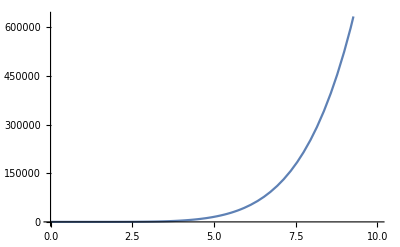

{{z→0},{z→0},{z→-a^(1/4)},{z→-ⅈ a^(1/4)},{z→ⅈ a^(1/4)},{z→a^(1/4)}}

```mathematica
Plot[z^6-z^2,{z,0,10}]
Solve[z^6-z^2 a==0,z]
```

```mathematica
Simplify[(√(z^2/l^2 fp + zds))/zds-(√(z^2/l^2 fm + zds))/zds/.zd[[1]]]
```

-(4 l^2 σ^2 σc^2 (√((z^2 (4 σ^2+(fm-fp) σc^2)^2)/(l^2 σ^2 σc^2))-√((z^2 (4 σ^2+(-fm+fp) σc^2)^2)/(l^2 σ^2 σc^2))))/(z^2 (16 σ^4-8 (fm+fp) σ^2 σc^2+(fm-fp)^2 σc^4))

```mathematica
Solve[√((1+q)^2)-√((1-q)^2)==0,q]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{q→0}}

#### Chowdhury derivation

```mathematica
Simplify[F Td^2 - Rd^2/F/.Td->1/F √(Rd^2 + F)]
```

1

```mathematica
zd =FullSimplify[Solve[√(z^2/l^2 fp + zds)-√(z^2/l^2 fm + zds)== z/l (2 σ)/σc,zds]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{zds→(z^2 (16 σ^4-8 (fm+fp) σ^2 σc^2+(fm-fp)^2 σc^4))/(16 l^2 σ^2 σc^2)}}

```mathematica
Simplify[((√(z^2/l^2 fp + zds)-√(z^2/l^2 fm + zds))^2-((fm z^2)/l^2+(fp z^2)/l^2+2 zds))^2==(a-((fm z^2)/l^2+(fp z^2)/l^2+2 zds))^2]
Solve[%,a]
```

a^2 l^3+((fm-fp)^2 z^4)/l==2 a l (fm z^2+fp z^2+2 l^2 zds)

{{a→(fm l z^2+fp l z^2+2 l^3 zds-2 √(fm fp l^2 z^4+fm l^4 z^2 zds+fp l^4 z^2 zds+l^6 zds^2))/l^3},{a→(fm l z^2+fp l z^2+2 l^3 zds+2 √(fm fp l^2 z^4+fm l^4 z^2 zds+fp l^4 z^2 zds+l^6 zds^2))/l^3}}

```mathematica
Clear[m]
κp = 1/m(ΔM -m^2/(2 R))
κm = 1/m(ΔM +m^2/(2 R))
Simplify[κp - κm]
Simplify[ (Tp /.Tp->κp/Fp) - (Tm /.Tm->κm/Fm)]
```

(-m^2/(2 R)+ΔM)/m

(m^2/(2 R)+ΔM)/m

-m/R

-(Fm m^2+Fp m^2-2 Fm R ΔM+2 Fp R ΔM)/(2 Fm Fp m R)

```mathematica
Clear[κp,κm]
FullSimplify[κp/Fp + κm/Fm /.κm ->R σ + κp]
```

κp/Fp+(κp+R σ)/Fm

```mathematica
Solve[√(Rd^2 + Fp)-√(Rd^2 + Fm)== 4 π R σ,Rd]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{Rd→-(√(Fm^2-2 Fm Fp+Fp^2-32 Fm π^2 R^2 σ^2-32 Fp π^2 R^2 σ^2+256 π^4 R^4 σ^4))/(8 π R σ)},{Rd→(√(Fm^2-2 Fm Fp+Fp^2-32 Fm π^2 R^2 σ^2-32 Fp π^2 R^2 σ^2+256 π^4 R^4 σ^4))/(8 π R σ)}}

```mathematica
DSolve[σ[x]+x σ'[x]==0,σ[x],x]
DSolve[σ[x]+x σ'[x]==V[x],σ[x],x]
```

{{σ[x]→C[1]/x}}

{{σ[x]→C[1]/x+(V[K[1]]K[1]1x)/x}}

#### Corrected tunneling rate after mistake fixes

```mathematica
zs = z/.Solve[z^6/(l^2 zh^4)-z^2 H^2==0,z][[6]]
Integrate[1/(√(z^6/(l^2 zh^4)-z^2 H^2)),{z,zs,∞}]
```

√H √l zh

ConditionalExpression[π/(4 H), Re[H]>0&&Im[H]==0&&Re[l]>0&&Im[l]==0&&Re[zh]>0&&Im[zh]==0]

```mathematica
Integrate[1/((1-z^4/zh^4)√(z^6/(l^2 zh^4)-z^2 H^2)),{z,zh-1,∞}]
```

$Aborted

```mathematica
Solve[z^6 l^2 HM^2 - z^2 l^2 H^2 + z^10==0,z]
```

{{z→0},{z→0},{z→-((-HM^2 l^2-√(l^2 (4 H^2+HM^4 l^2)))^(1/4))/2^(1/4)},{z→-(ⅈ (-HM^2 l^2-√(l^2 (4 H^2+HM^4 l^2)))^(1/4))/2^(1/4)},{z→(ⅈ (-HM^2 l^2-√(l^2 (4 H^2+HM^4 l^2)))^(1/4))/2^(1/4)},{z→((-HM^2 l^2-√(l^2 (4 H^2+HM^4 l^2)))^(1/4))/2^(1/4)},{z→-((-HM^2 l^2+√(l^2 (4 H^2+HM^4 l^2)))^(1/4))/2^(1/4)},{z→-(ⅈ (-HM^2 l^2+√(l^2 (4 H^2+HM^4 l^2)))^(1/4))/2^(1/4)},{z→(ⅈ (-HM^2 l^2+√(l^2 (4 H^2+HM^4 l^2)))^(1/4))/2^(1/4)},{z→((-HM^2 l^2+√(l^2 (4 H^2+HM^4 l^2)))^(1/4))/2^(1/4)}}

```mathematica
Solve[z^6 HM^2 - z^2 H^2==0,z]
```

{{z→0},{z→0},{z→-(√H)/(√HM)},{z→-(ⅈ √H)/(√HM)},{z→(ⅈ √H)/(√HM)},{z→(√H)/(√HM)}}

```mathematica
Series[√(1+1/4 z^2),{z,∞,1}]
```

z/2+1/z+O[1/z]^2

```mathematica
Series[√(1+1/4(σc^2 -  σ^2)/□),{z,∞,1}]
```

#### correction to nz

```mathematica
GDD
```

{{-(L^2 (z^4-zh^4))/z^6,0,0,0,0},{0,L^2/z^2,0,0,0},{0,0,L^2/z^2,0,0},{0,0,0,L^2/z^2,0},{0,0,0,0,(L^2 z^2)/(z^4-zh^4)}}

```mathematica
FullSimplify[√(-1/GDD[[1,1]](1+zd^2 GDD[[5,5]]))]
FullSimplify[PowerExpand[√(1/((L^2 fz)/z^2)(1+zd^2 L^2/(z^2 fz)))]]
```

√((z^6 (z^4+L^2 z^2 zd^2-zh^4))/(L^2 (z^4-zh^4)^2))

(z √(1+(L^2 zd^2)/(fz z^2)))/(√fz L)

```mathematica
(zh^4/(l^2 z^2)-z^2 H^2)
```

```mathematica
zs = zh/(√(H L))
Integrate[z L/zh^2 √(M(1-z^4 (H^2 L^2)/zh^4)),{z,zs,∞} ]
```

zh/(√(H L))

$Aborted

```mathematica
Integrate[1/(z L M √(Α/(ρM-ρω)-z^4 H^2 L^2)),z]
```

-(√(ρM-ρω) ArcTanh[(√(ρM-ρω) √((Α+H^2 L^2 z^4 (-ρM+ρω))/(ρM-ρω)))/(√Α)])/(2 L M √Α)

```mathematica
Integrate[1/(z L M √(zh^4-z^4 H^2 L^2)),{z,zs,∞}]
```

ConditionalExpression[-(ⅈ π)/(4 L M zh^2), zh≠0&&zh/(√(H L))≥0]

```mathematica
Integrate[L/(√(zh^4-u^2 H^2 L^2)),u]
FullSimplify[%]
```

ArcTan[(H L u)/(√(-H^2 L^2 u^2+zh^4))]/H

ArcTan[(H L u)/(√(-H^2 L^2 u^2+zh^4))]/H

1/H(ρω ArcTan[(H L u)/(√(-H^2 L^2 u^2+A/(ρM-ρω)))]-(-H L u (ρM-ρω) (A+H^2 L^2 u^2 (-ρM+ρω))+(-A+2 H^2 L^2 u^2 ρM) √(ρM-ρω) √(A+H^2 L^2 u^2 (-ρM+ρω)) ArcTan[(√(A+H^2 L^2 u^2 (-ρM+ρω)))/(H L u √(ρM-ρω))])/(2 H^2 L^2 u^2 (-ρM+ρω) √((A+H^2 L^2 u^2 (-ρM+ρω))/(ρM-ρω))))

```mathematica
zs = zh/(√(H L))
(L z)/(√(-(zh^4-z^4 H^2 L^2)))/.zh^4->A/(ρM - ρω)
Integrate[%,ρω]
Integrate[%,{z,zs,∞}]
```

zh/(√(H L))

(L z)/(√(H^2 L^2 z^4-A/(ρM-ρω)))

(H L z^2 (-ρM+ρω) √(H^2 L^2 z^4+A/(-ρM+ρω))-A ArcTanh[(√(H^2 L^2 z^4+A/(-ρM+ρω)))/(H L z^2)])/(H^3 L^2 z^5)

$Aborted

```mathematica
Integrate[z^-7,z]
```

-1/(6 z^6)

```mathematica
Series[1 - (1-ϵ)^(3/2),{ϵ,0,1}]
```

(3 ϵ)/2+O[ϵ]^2

```mathematica
Series[1/(√(1-(z+I ϵ)^2)),{ϵ,0,1}]
Integrate[1/(√(1-z^2)),{z,-1,1}]
Integrate[z/((1-z^2)^(3/2)),{z,-1,1}]
```

1/(√(1-z^2))+(ⅈ z ϵ)/((1-z^2)^(3/2))+O[ϵ]^2

π

Integrate::idiv: Integral of z/((1-z^2)^(3/2)) does not converge on {-1,1}.

∫_-1^1 z/((1-z^2)^(3/2))ⅆz

#### Panleve coordinates - proper time

```mathematica
f[z_]:=1 - zh^4/z^4
met5D = l^2/z^2{{-f[z],0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1/f[z]}}
x= {t,v,y,w,z};

(*Painleve*)
XPL= {t+ Integrate[z^2/(zh^2 f[z]),z],v,y,w,z};
JXxPL=Table[D[XPL[[i]],x[[j]]],{i,5},{j,5}];
gPL = FullSimplify[Transpose[JXxPL].met5D.JXxPL]
FullSimplify[Inverse[JXxPL]];

(*Proper time*)
XPt= {√f[z] t,v,y,w,z};
JXxPt=Table[D[XPt[[i]],x[[j]]],{i,5},{j,5}];
gPt = FullSimplify[Transpose[JXxPt].met5D.JXxPt]
FullSimplify[Inverse[JXxPt]];
```

{{(l^2 (-1+zh^4/z^4))/z^2,0,0,0,0},{0,l^2/z^2,0,0,0},{0,0,l^2/z^2,0,0},{0,0,0,l^2/z^2,0},{0,0,0,0,l^2/(z^2 (1-zh^4/z^4))}}

{{(l^2 (-z^4+zh^4))/z^6,0,0,0,-l^2/zh^2},{0,l^2/z^2,0,0,0},{0,0,l^2/z^2,0,0},{0,0,0,l^2/z^2,0},{-l^2/zh^2,0,0,0,-(l^2 z^2)/zh^4}}

{{-(l^2 (z^4-zh^4)^2)/z^10,0,0,0,(2 l^2 t zh^4 (-1+zh^4/z^4))/z^7},{0,l^2/z^2,0,0,0},{0,0,l^2/z^2,0,0},{0,0,0,l^2/z^2,0},{(2 l^2 t zh^4 (-1+zh^4/z^4))/z^7,0,0,0,(l^2 (z^14-4 t^2 z^4 zh^8+4 t^2 zh^12))/(z^12 (z^4-zh^4))}}

```mathematica
FullSimplify[D[Integrate[z^2/(zh^2 f[z]),z],z]]
```

z^6/(z^4 zh^2-zh^6)

### Time dep GW

```mathematica
met5D = l^2/z^2{{g[z],0,0,0,0},{0,1,0,0,0},{0,0,1/g[z],0,0},{0,0,0,r^2,0},{0,0,0,0,r^2 Sin[θ]^2}}
X= {t,r,l^2/ρ,θ,ϕ};
x= {t,r,ρ,θ,ϕ};
JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,5}];
gρ = Simplify[Transpose[JXx].(met5D/.g[z]->1-z^4/zh^4/.z->l^2/ρ/.zh->l^2/ρh).JXx ];
gρ //MatrixForm 
Simplify[Det[gρ]]

X= {t,r,ρh y^(1/4),θ,ϕ};
x= {t,r,y,θ,ϕ};
JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,5}];
gy = Simplify[Transpose[JXx].(gρ/.ρ->ρh y^(1/4)).JXx ];
gy //MatrixForm 
Simplify[Det[gy]]

g5y = Det[gy];
ϕeqn =Simplify[-(1/(√g5y)D[√g5y Inverse[gy][[3,3]]D[ϕ[y],y],y]-m^2 ϕ[y])l^2]==0
(*Simplify[ϕeqn/.ρ->y/ρh/.ϕ[ρh-ρ]->ϕ[ρ]]*)
ϕsol=DSolve[ϕeqn,ϕ[y],y];
(*ϕsol=DSolve[ϕeqn,ϕ[1/ρ],ρ];*)
ϕos1=ϕ[y]/.ϕsol[[1]]/.{C[1]->1,C[2]->0}
ϕos2=ϕ[y]/.ϕsol[[1]]/.{C[1]->0,C[2]->1}
```

{{(l^2 g[z])/z^2,0,0,0,0},{0,l^2/z^2,0,0,0},{0,0,l^2/(z^2 g[z]),0,0},{0,0,0,(l^2 r^2)/z^2,0},{0,0,0,0,(l^2 r^2 Sin[θ]^2)/z^2}}

((ρ^4-ρh^4)/(l^2 ρ^2) | 0 | 0 | 0 | 0
0 | ρ^2/l^2 | 0 | 0 | 0
0 | 0 | (l^2 ρ^2)/(ρ^4-ρh^4) | 0 | 0
0 | 0 | 0 | (r^2 ρ^2)/l^2 | 0
0 | 0 | 0 | 0 | (r^2 ρ^2 Sin[θ]^2)/l^2)

(r^4 ρ^6 Sin[θ]^2)/l^6

(((-1+y) ρh^2)/(l^2 √y) | 0 | 0 | 0 | 0
0 | (√y ρh^2)/l^2 | 0 | 0 | 0
0 | 0 | l^2/(16 (-1+y) y) | 0 | 0
0 | 0 | 0 | (r^2 √y ρh^2)/l^2 | 0
0 | 0 | 0 | 0 | (r^2 √y ρh^2 Sin[θ]^2)/l^2)

(r^4 ρh^8 Sin[θ]^2)/(16 l^6)

l^2 m^2 ϕ[y]-16 ((-1+2 y) ϕ'[y]+(-1+y) y ϕ''[y])==0

LegendreP[1/4 (-2+√(4+l^2 m^2)),-1+2 y]

LegendreQ[1/4 (-2+√(4+l^2 m^2)),-1+2 y]

```mathematica
DSolve[ϕt''[t] == Λ gtt ϕt[t],ϕt[t],t]
```

{{ϕt[t]→ⅇ^(√gtt t √Λ) C[1]+ⅇ^(-√gtt t √Λ) C[2]}}

```mathematica
DSolve[ϕt''[t] == 0,ϕt[t],t]
```

{{ϕt[t]→C[1]+t C[2]}}

### Non zero potential on brane

#### Metric

```mathematica
met5D = l^2/z^2{{g[z],0,0,0,0},{0,1,0,0,0},{0,0,1/g[z],0,0},{0,0,0,1,0},{0,0,0,0,1}}
X= {t,r,l^2/ρ,θ,ϕ};
x= {t,r,ρ,θ,ϕ};
JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,5}];
gρ = Simplify[Transpose[JXx].(met5D/.g[z]->1-z^4/zh^4/.z->l^2/ρ/.zh->l^2/ρh).JXx ]
gρ //MatrixForm 
Simplify[Det[gρ]]

X= {t,r,ρh y^(1/4),θ,ϕ};
x= {t,r,y,θ,ϕ};
JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,5}];
gy = Simplify[Transpose[JXx].(gρ/.ρ->ρh y^(1/4)).JXx ];
gy //MatrixForm 
Simplify[Det[gy]]
```

{{(l^2 g[z])/z^2,0,0,0,0},{0,l^2/z^2,0,0,0},{0,0,l^2/(z^2 g[z]),0,0},{0,0,0,l^2/z^2,0},{0,0,0,0,l^2/z^2}}

{{(ρ^4-ρh^4)/(l^2 ρ^2),0,0,0,0},{0,ρ^2/l^2,0,0,0},{0,0,(l^2 ρ^2)/(ρ^4-ρh^4),0,0},{0,0,0,ρ^2/l^2,0},{0,0,0,0,ρ^2/l^2}}

((ρ^4-ρh^4)/(l^2 ρ^2) | 0 | 0 | 0 | 0
0 | ρ^2/l^2 | 0 | 0 | 0
0 | 0 | (l^2 ρ^2)/(ρ^4-ρh^4) | 0 | 0
0 | 0 | 0 | ρ^2/l^2 | 0
0 | 0 | 0 | 0 | ρ^2/l^2)

ρ^6/l^6

(((-1+y) ρh^2)/(l^2 √y) | 0 | 0 | 0 | 0
0 | (√y ρh^2)/l^2 | 0 | 0 | 0
0 | 0 | l^2/(16 (-1+y) y) | 0 | 0
0 | 0 | 0 | (√y ρh^2)/l^2 | 0
0 | 0 | 0 | 0 | (√y ρh^2)/l^2)

ρh^8/(16 l^6)

```mathematica
gy[[3,3]]
```

l^2/(16 (-1+y) y)

```mathematica
ϕa[y_]:=Aa P[y]+Ba Q[y]
ϕb[y_]:=Ab P[y]
Solve[ϕa[y]==ϕ,Aa]
Solve[ϕb[y]==ϕ,Ab]
1/gy[[3,3]] δ (ϕa'[y]-ϕb'[y]) + δ/(√gy[[3,3]])4  λ ϕ(ϕ^2 - v0^2)/.%[[1]]/.%%[[1]]
FullSimplify[Solve[%==0,Ba]]
FullSimplify[%/.ϕ->Ab P[y]]
```

{{Aa→(ϕ-Ba Q[y])/P[y]}}

{{Ab→ϕ/P[y]}}

(16 δ λ ϕ (-v0^2+ϕ^2))/(√(l^2/((-1+y) y)))+1/l^2 16 (-1+y) y δ (-(ϕ P'[y])/P[y]+((ϕ-Ba Q[y]) P'[y])/P[y]+Ba Q'[y])

{{Ba→(√(l^2/((-1+y) y)) λ (v0-ϕ) ϕ (v0+ϕ) P[y])/(-Q[y] P'[y]+P[y] Q'[y])}}

{{Ba→(Ab √(l^2/((-1+y) y)) λ P[y]^2 (v0-Ab P[y]) (v0+Ab P[y]))/(-Q[y] P'[y]+P[y] Q'[y])}}

```mathematica
λ(ϕ^2 - v0^2)^2/.ϕ->Ab P[y]
```

λ (-v0^2+Ab^2 P[y]^2)^2

```mathematica
ϕa[y_]:=Aa P[y]+Ba Q[y]
ϕb[y_]:=Ab P[y]
Solve[ϕa[y]==ϕ,Aa]
Solve[ϕb[y]==ϕ,Ab]
1/gy[[3,3]] δ (ϕa'[y]-ϕb'[y]) + δ/(√gy[[3,3]])4  λ ϕ l^4(ϕ^2 - l^-3 v0^2)/.%[[1]]/.%%[[1]]
FullSimplify[Solve[%==0,Ba]]
FullSimplify[%/.ϕ->Ab P[y]]
```

{{Aa→(ϕ-Ba Q[y])/P[y]}}

{{Ab→ϕ/P[y]}}

(16 l^4 δ λ ϕ (-v0^2/l^3+ϕ^2))/(√(l^2/((-1+y) y)))+1/l^2 16 (-1+y) y δ (-(ϕ P'[y])/P[y]+((ϕ-Ba Q[y]) P'[y])/P[y]+Ba Q'[y])

{{Ba→(l √(l^2/((-1+y) y)) λ ϕ (v0^2-l^3 ϕ^2) P[y])/(-Q[y] P'[y]+P[y] Q'[y])}}

{{Ba→(Ab l √(l^2/((-1+y) y)) λ P[y]^2 (v0^2-Ab^2 l^3 P[y]^2))/(-Q[y] P'[y]+P[y] Q'[y])}}

```mathematica
Solve[z^4-zh^4==0,z]
```

{{z→-zh},{z→-ⅈ zh},{z→ⅈ zh},{z→zh}}

```mathematica
Clear[V,ϕa,ϕb,y]
ϕa[y_]:=Aa P[y]+Ba Q[y]
ϕb[y_]:=Ab P[y]
Solve[ϕa[y]==ϕ,Aa]
Solve[ϕb[y]==ϕ,Ab]
2/gyy δ (ϕa'[y]-ϕb'[y]) + δ/(√gyy)Vp/.%[[1]]/.%%[[1]]
FullSimplify[Solve[%==0,Ba]]
FullSimplify[%/.ϕ->Ab P[y]]
```

{{Aa→(ϕ-Ba Q[y])/P[y]}}

{{Ab→ϕ/P[y]}}

(Vp δ)/(√gyy)+(2 δ (-(ϕ P'[y])/P[y]+((ϕ-Ba Q[y]) P'[y])/P[y]+Ba Q'[y]))/gyy

{{Ba→(√gyy Vp P[y])/(2 Q[y] P'[y]-2 P[y] Q'[y])}}

{{Ba→(√gyy Vp P[y])/(2 Q[y] P'[y]-2 P[y] Q'[y])}}

#### comparison to kraus

```mathematica
Simplify[R^4(z^6 HM - z^2 H + z^10/.z->1/R)]
Simplify[R[τ]^4 D[1/R[τ],τ]^2]
```

1/R^6+HM/R^2-H R^2

R'[τ]^2

```mathematica
f[z]
Clear[zd]
GDD
FullSimplify[√(1/(l^2/z^2 g[z])(1 + l^2/z^2 rd^2 + l^2/(z^2 g[z])zd^2))]
```

1-zh^4/z^4

{{(L^2 (-1+z^4/zh^4))/z^2,0,0,0,0},{0,L^2/z^2,0,0,0},{0,0,L^2/z^2,0,0},{0,0,0,L^2/z^2,0},{0,0,0,0,L^2/(z^2 (1-z^4/zh^4))}}

√((zd^2+(rd^2+z^2/l^2) g[z])/g[z]^2)

#### Find profile vectors

```mathematica
Outer[Times,{vt,vr,vz},{nt,nr,nz}]
```

{{nt vt,nr vt,nz vt},{nt vr,nr vr,nz vr},{nt vz,nr vz,nz vz}}

```mathematica
Clear[v,u]
gtemp = DiagonalMatrix[{gtt,grr,0,0,gzz}]
v = {vt,vr,0,0,vz};
n = {nt,nr,0,0,nz};
u ={ut,ur,0,0,uz};
(*Solve[v.GDD.n==0&&v.GDD.v==1&&v.GDD.u==1,{vt,vr,vz}]*)
Simplify[Solve[v.gtemp.n==0&&v.gtemp.v==1&&v.gtemp.u==1,{vt,vr,vz}]]
```

{{gtt,0,0,0,0},{0,grr,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,gzz}}

```mathematica
{v.GDD.n==0,v.GDD.v==1,n.GDD.n==1}
```

{(L^2 nr vr)/z^2+(L^2 nz vz)/(z^2 (1-z^4/zh^4))+(L^2 nt vt (-1+z^4/zh^4))/z^2==0,(L^2 vr^2)/z^2+(L^2 vz^2)/(z^2 (1-z^4/zh^4))+(L^2 vt^2 (-1+z^4/zh^4))/z^2==1,(L^2 nr^2)/z^2+(L^2 nz^2)/(z^2 (1-z^4/zh^4))+(L^2 nt^2 (-1+z^4/zh^4))/z^2==1}

```mathematica
vrsol =Solve[1 == gtt vt^2 + grr vr^2,vr]
```

{{vr→-(√(1-gtt vt^2))/(√grr)},{vr→(√(1-gtt vt^2))/(√grr)}}

```mathematica
Solve[1 == gtt nt^2 + grr (-gtt/grr √(grr/(1-gtt))nt)^2 + gzz nz^2,nz]
```

{{nz→-(√(-1+gtt+gtt nt^2))/(√(-1+gtt) √gzz)},{nz→(√(-1+gtt+gtt nt^2))/(√(-1+gtt) √gzz)}}

```mathematica
vtsol = Solve[0 == ur √(grr (1-gzz vt^2))+gtt ut vt,vt][[1]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{vt→-(√grr ur)/(√(grr gzz ur^2+gtt^2 ut^2))}

```mathematica
vr/.vrsol/.vtsol
```

{-(√(1-(grr gtt ur^2)/(grr gzz ur^2+gtt^2 ut^2)))/(√grr),(√(1-(grr gtt ur^2)/(grr gzz ur^2+gtt^2 ut^2)))/(√grr)}

```mathematica
Solve[gtt nt vt + grr nr vr ==0,nr]
nrsol =%/.vrsol[[1,1]]
```

{{nr→-(gtt nt vt)/(grr vr)}}

{{nr→(gtt nt vt)/(√grr √(1-gtt vt^2))}}

```mathematica
nzsol = Solve[1 == gtt nt^2 + grr (nr/.nrsol)^2+gzz nz^2 ,nz]
```

{{nz→-(√(-1+gtt nt^2+gtt vt^2))/(√gzz √(-1+gtt vt^2))},{nz→(√(-1+gtt nt^2+gtt vt^2))/(√gzz √(-1+gtt vt^2))}}

```mathematica
ntsol = FullSimplify[Solve[(gtt ut nt+ grr ur nr + gzz uz nz/.nrsol/.nzsol[[1]]) == 0, nt]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{nt→-(√(-gzz uz^2 (-1+gtt vt^2) (gzz uz^2+grr gtt ur^2 vt^2+gtt ut (ut-gtt ut vt^2-2 √grr ur vt √(1-gtt vt^2)))))/(√gtt √((gtt ut^2+gzz uz^2)^2-2 gtt (grr ur^2 (gtt ut^2-gzz uz^2)+gtt ut^2 (gtt ut^2+gzz uz^2)) vt^2+gtt^2 (grr ur^2+gtt ut^2)^2 vt^4))},{nt→(√(-gzz uz^2 (-1+gtt vt^2) (gzz uz^2+grr gtt ur^2 vt^2+gtt ut (ut-gtt ut vt^2-2 √grr ur vt √(1-gtt vt^2)))))/(√gtt √((gtt ut^2+gzz uz^2)^2-2 gtt (grr ur^2 (gtt ut^2-gzz uz^2)+gtt ut^2 (gtt ut^2+gzz uz^2)) vt^2+gtt^2 (grr ur^2+gtt ut^2)^2 vt^4))}}

```mathematica
nt/.ntsol/.nrsol
```

```mathematica
(gtt ut nt+ grr ur nr + gzz uz nz/.nrsol/.nzsol)
```

{{gtt nt ut+(√grr gtt nt ur vt)/(√(1-gtt vt^2))-(√gzz uz √(-1+gtt nt^2+gtt vt^2))/(√(-1+gtt vt^2))},{gtt nt ut+(√grr gtt nt ur vt)/(√(1-gtt vt^2))+(√gzz uz √(-1+gtt nt^2+gtt vt^2))/(√(-1+gtt vt^2))}}

What a mess! we just care about normal, so repeat this imposing a condition on n and ignoring v

```mathematica
Clear[nzsol,ntsol,p]
nzsol =Solve[1 == gtt nt^2 + gzz nz^2 ,nz];
ntsol = Solve[0 == gzz uz (nz/.nzsol[[1]])+gtt ut nt,nt][[2]];
ntt = nt/.ntsol;
nzz = nz/.nzsol[[2]]/.ntsol ;
Simplify[nzz/.{gzz->1/g[p],gtt->-g[p],ut->1/g[p] √((1+p^2/l^2 rd^2)g[p]+pd^2),uz->pd}]
Simplify[ntt /. {gzz->1/g[p],gtt->-g[p],ut->1/g[p] √((1+p^2/l^2 rd^2)g[p]+pd^2),uz->pd}]
Simplify[ut^2 gtt + uz^2 gzz/. {gzz->1/g[p],gtt->-g[p],ut->1/g[p] √((1+p^2/l^2 rd^2)g[p]+pd^2),uz->pd}]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

(√(1+(l^2 pd^2)/((l^2+p^2 rd^2) g[p])))/(√(1/g[p]))

(pd √(1/g[p]))/(√(-1-(p^2 rd^2)/l^2) √(-g[p]))

-1-(p^2 rd^2)/l^2

```mathematica
PowerExpand[Simplify[ntt /.{gzz->l^2/(z^2 g[z]),gtt->-l^2/z^2 g[z],uz->zd,ut->1/g[z] √((z^2/l^2+rd^2)g[z]+zd^2)}]]/.g[z]->f[z]
FullSimplify[PowerExpand[Simplify[nzz /.{gzz->l^2/(z^2 g[z]),gtt->-l^2/z^2 g[z],uz->zd,ut->1/g[z] √((z^2/l^2+rd^2)g[z]+zd^2)}]]/.g[z]->f[z]]
nnew = {%%,0,0,0,%} 
FullSimplify[nnew.GDD.nnew]
```

-(ⅈ zd)/(√(-1-(l^2 rd^2)/z^2) (1-z^4/zh^4))

-(z √(1+(l^2 zd^2)/((l^2 rd^2+z^2) (1-z^4/zh^4))) √(1-z^4/zh^4))/l

{-(ⅈ zd)/(√(-1-(l^2 rd^2)/z^2) (1-z^4/zh^4)),0,0,0,-(z √(1+(l^2 zd^2)/((l^2 rd^2+z^2) (1-z^4/zh^4))) √(1-z^4/zh^4))/l}

L^2/l^2

```mathematica
f[z_]:=1-z^4/zh^4
```

```mathematica
nold={zd/g[z],0,0,0,√(z^2/l^2 g[z]+zd^2)}
FullSimplify[nold.GDD.nold/.g[z]->f[z]]
```

{zd/g[z],0,0,0,√(zd^2+(z^2 g[z])/l^2)}

L^2/l^2

```mathematica
f[z]
```

1-zh^4/z^4

```mathematica
Γ[[5,;;,;;]]
```

{{-1/z+z^7/zh^8,0,0,0,0},{0,1/z-z^3/zh^4,0,0,0},{0,0,1/z-z^3/zh^4,0,0},{0,0,0,1/z-z^3/zh^4,0},{0,0,0,0,(-3 z^4+zh^4)/(z^5-z zh^4)}}

```mathematica
Simplify[1/(2 GDD[[5,5]])D[GDD[[5,5]],z]]
Simplify[1/(2 GDD[[5,5]])D[GDD[[1,1]],z]]
```

(-3 z^4+zh^4)/(z^5-z zh^4)

1/z-z^7/zh^8

```mathematica
FullSimplify[z''[τ]+(z^2 g[z])/(2 l^2)(κ^2/g[z]^2 D[l^2/z^2 g[z],z]-z'[τ]^2 D[l^2/(z^2 g[z]),z])]
temp =D[z[τ],τ]FullSimplify[PowerExpand[ %/κ/.κ->√(z^2/l^2 g[z]+z'[τ]^2)]]
(*FullSimplify[% /. g[z]->f[z]]*)
```

(g'[z] (κ^2+z'[τ]^2))/(2 g[z])+(-κ^2+z'[τ]^2+z z''[τ])/z

(z'[τ] ((z (-2 g[z]+z g'[z]))/(2 l^2)+(g'[z] z'[τ]^2)/g[z]+z''[τ]))/(√((z^2 g[z])/l^2+z'[τ]^2))

```mathematica
FullSimplify[z'[τ]D[√(z^2/l^2 g[z]+z'[τ]^2),z] + 2 (z'[τ] z''[τ])/(√(z^2/l^2 g[z]+z'[τ]^2))]
FullSimplify[% - temp]
%/.g[z]->f[z]
FullSimplify[% /. g[z]->f[z]]
```

(z'[τ] (2 z g[z]+z^2 g'[z]+4 l^2 z''[τ]))/(2 l^2 √((z^2 g[z])/l^2+z'[τ]^2))

(z'[τ] (2 z g[z]^2-l^2 g'[z] z'[τ]^2+l^2 g[z] z''[τ]))/(l^2 g[z] √((z^2 g[z])/l^2+z'[τ]^2))

(z'[τ] (2 z (1-z^4/zh^4)^2-l^2 g'[z] z'[τ]^2+l^2 (1-z^4/zh^4) z''[τ]))/(l^2 (1-z^4/zh^4) √((z^2 (1-z^4/zh^4))/l^2+z'[τ]^2))

(z'[τ] (2 z (-1+z^4/zh^4)^2-l^2 g'[z] z'[τ]^2+l^2 (1-z^4/zh^4) z''[τ]))/(l^2 (1-z^4/zh^4) √((z^2 (1-z^4/zh^4))/l^2+z'[τ]^2))

```mathematica
FullSimplify[1/GDD[[5,5]] D[l^2/z^2 f[z],z]]
FullSimplify[1/GDD[[5,5]] D[l^2/(z^2 f[z]),z]]
FullSimplify[%-%%]
```

(2 l^2 (z^8-zh^8))/(L^2 z zh^8)

(2 l^2 (-3 z^4+zh^4))/(L^2 (z^5-z zh^4))

(2 l^2 z^3 (z^8-z^4 zh^4+2 zh^8))/(L^2 zh^8 (-z^4+zh^4))

```mathematica
Simplify[D[Log[GDD[[1,1]]],z]]
```

(2 (z^4+zh^4))/(z^5-z zh^4)

#### Potential Analysis

This is in units of the planck length

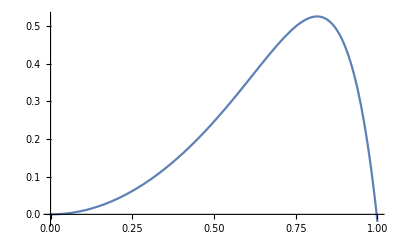

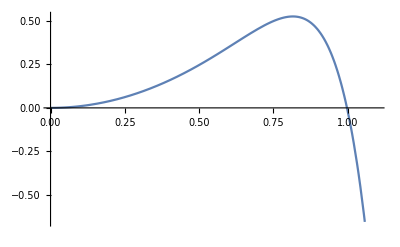

```mathematica
Plot[-(z^6 HM - z^2 H + z^10)/.{HM -> 0.01,H->0.99},{z,0,1}]
Plot[-(z^6 HM - z^2 H + z^10)/.{HM -> 0.01,H->0.99},{z,0,1.1}]
```

```mathematica
ϕo
```

```mathematica
Manipulate[Plot[-(z^6 4((r+h )-h/2) - z^2 (1-h^2) + z^10),{z,0,10}],{h,-1,0.01},{r,0,0.1}]
```

```mathematica
ϕos1type3 = PowerExpand[Simplify[LegendreP[1/4 (-2+√(4+l^2 m^2)),0,3,-1+2 y]/.m->(√(ϵ(4+ϵ)))/l]]/.y->(zh/z)^4
ϕos2type3 =PowerExpand[Simplify[LegendreQ[1/4 (-2+√(4+l^2 m^2)),0,3,-1+2 y]/.m->(√(ϵ(4+ϵ)))/l]]/.y->(zh/z)^4
Vϕ[zt_,zht_,n_]:=ϕos1type3^n/.{zh->zht,z->zt,ϵ->0.1}
```

LegendreP[ϵ/4,-1+(2 zh^4)/z^4]

LegendreQ[ϵ/4,0,3,-1+(2 zh^4)/z^4]

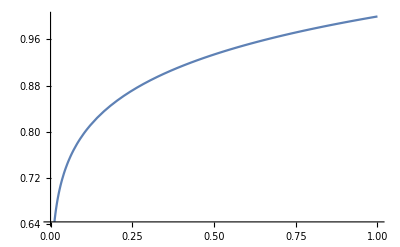

```mathematica
Plot[ϕos1type3/.{zh->1,ϵ->-0.1},{z,0,1}]
```

```mathematica
Vϕ[1,4,4]
```

1.74793

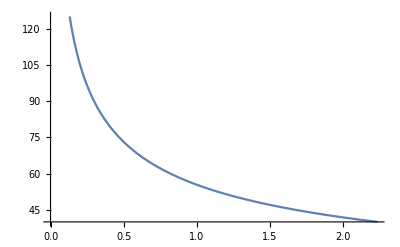

```mathematica
Plot[λ0 Vϕ[z,(σc/(4 ρM))^(1/4),nϕ]/.ρrepl,{z,0,(σc/(4 ρM))^(1/4)/.ρrepl}]
```

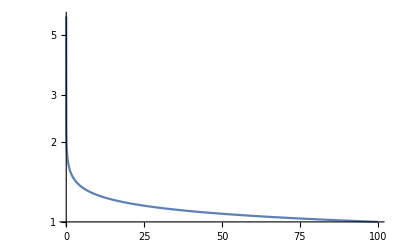

```mathematica
LogPlot[ϕos1type3/.{ϵ->0.1,zh->100},{z,0,100},PlotRange->All]
```

Small curvature expansion is l/M<<1, which implies 1/l<1/l_P

```mathematica
Vϕ[1]
```

LegendreP[0.025,-1+2 zh^4]^4

```mathematica
Vϕ[z,(σc/(4 ρM))^(1/4)]/.{σc->1,ρM->0.001,ρω->0.00001}
```

LegendreP[0.025,-1+500./z^4]^4

Target z corresponding to a hierarchy of planck over higgs mass (units of l=1)

```mathematica
z/.Solve[10^-17/1== z^5,z][[2]]
```

1/(1000 10^(2/5))

```mathematica
Solve[M^3 l(z1^5/l^5-z0^5/l^5)==M4,z1]
```

{{z1→((l^4 M4+M^3 z0^5)^(1/5))/M^(3/5)},{z1→-((-1)^(1/5) (l^4 M4+M^3 z0^5)^(1/5))/M^(3/5)},{z1→((-1)^(2/5) (l^4 M4+M^3 z0^5)^(1/5))/M^(3/5)},{z1→-((-1)^(3/5) (l^4 M4+M^3 z0^5)^(1/5))/M^(3/5)},{z1→((-1)^(4/5) (l^4 M4+M^3 z0^5)^(1/5))/M^(3/5)}}

Metric updates as we change the energy density of the brane

2.23607

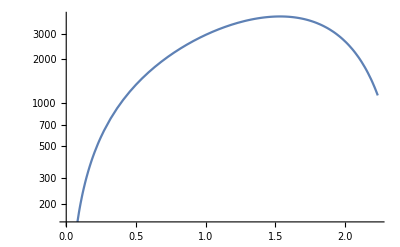

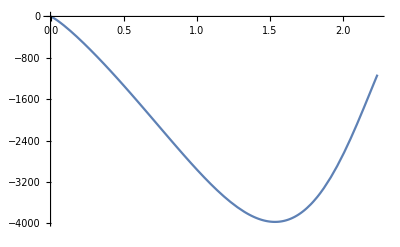

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
ρrepl ={σc->1,ρM->0.01,ρω->0.001,λ0->40,nϕ->4};
Print[(σc/(4 ρM))^(1/4)/.ρrepl]
LogPlot[(z^6 4(ρM/σc -(ρω+λ0 Vϕ[z,(σc/(4 ρM))^(1/4),nϕ])/(2 σc)) - z^2 (1-((ρω+λ0 Vϕ[z,(σc/(4 ρM))^(1/4),nϕ])/σc)^2) + z^10)/.ρrepl,{z,0,(σc/(4 ρM))^(1/4)/.ρrepl}]
Plot[-(z^6 4(ρM/σc -(ρω+λ0 Vϕ[z,(σc/(4 ρM))^(1/4),nϕ])/(2 σc)) - z^2 (1-((ρω+λ0 Vϕ[z,(σc/(4 ρM))^(1/4),nϕ])/σc)^2) + z^10)/.ρrepl,{z,0,(σc/(4 ρM))^(1/4)/.ρrepl}]
Plot[λ0 Vϕ[z,(σc/(4 ρM))^(1/4),nϕ]/.ρrepl,{z,0,(σc/(4 ρM))^(1/4)/.ρrepl}]
```

A potential for small λ0 -> we see we can get a local minimum of the potential at small values of z, but which is seperated by a small potential barrier. 

This situation is attractive because it could lead to realistic hierarchies, but is unattractive because it would require to tunneling events, which would significantly supress this channel.

7.07107

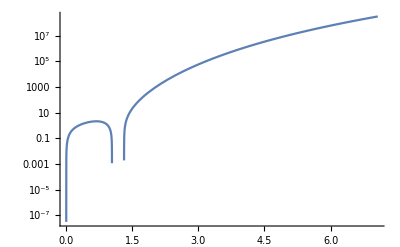

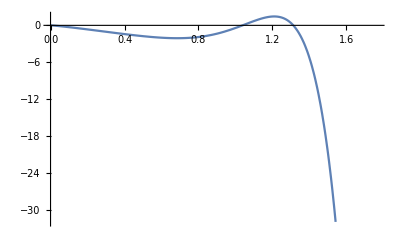

```mathematica
ρrepl ={σc->1,ρM->0.0001,ρω->0.000001,λ0->1,nϕ->4};
Print[(σc/(4 ρM))^(1/4)/.ρrepl]
LogPlot[(z^6 4(ρM/σc -(ρω+λ0 Vϕ[z,(σc/(4 ρM))^(1/4),nϕ])/(2 σc)) - z^2 (1-((ρω+λ0 Vϕ[z,(σc/(4 ρM))^(1/4),nϕ])/σc)^2) + z^10)/.ρrepl,{z,0,(σc/(4 ρM))^(1/4)/.ρrepl}]
Plot[-(z^6 4(ρM/σc -(ρω+λ0 Vϕ[z,(σc/(4 ρM))^(1/4),nϕ])/(2 σc)) - z^2 (1-((ρω+λ0 Vϕ[z,(σc/(4 ρM))^(1/4),nϕ])/σc)^2) + z^10)/.ρrepl,{z,0,1/4(σc/(4 ρM))^(1/4)/.ρrepl}]
(*Plot[λ0 Vϕ[z,(σc/(4 ρM))^(1/4),nϕ]/.ρrepl,{z,0,(σc/(4 ρM))^(1/4)/.ρrepl}]
Plot[(1-((ρω+λ0 Vϕ[z,(σc/(4 ρM))^(1/4),nϕ])/σc)^2) /.ρrepl,{z,0,(σc/(4 ρM))^(1/4)/.ρrepl}]*)
```

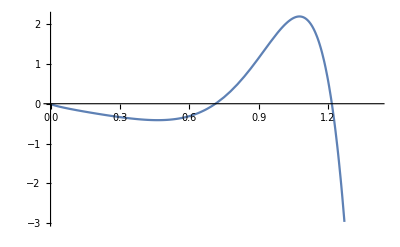

```mathematica
ρrepl ={σc->1,ρM->0.0001,ρω->0.000001,λ0->1,nϕ->1};
Plot[-(1+D[Log[zt (ρω+λ0 Vϕ[zt,(σc/(4 ρM))^(1/4),nϕ])],zt]/.zt->z)(z^6 4(ρM/σc -(ρω+λ0 Vϕ[z,(σc/(4 ρM))^(1/4),nϕ])/(2 σc)) - z^2 (1-((ρω+λ0 Vϕ[z,(σc/(4 ρM))^(1/4),nϕ])/σc)^2) + z^10)/.ρrepl,{z,0,1/5(σc/(4 ρM))^(1/4)/.ρrepl}]
```

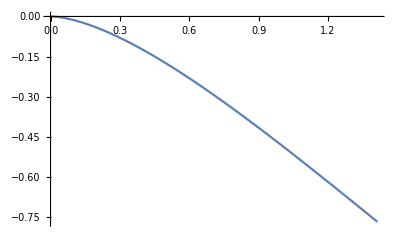

```mathematica
Plot[-(z^6 4(ρM/σc ) - z^2 (1-((ρω+λ0 Vϕ[z,(σc/(4 ρM))^(1/4),nϕ])/σc)^2) )/.ρrepl,{z,0,1/5(σc/(4 ρM))^(1/4)/.ρrepl}]
```

```mathematica
1
```

7.07107

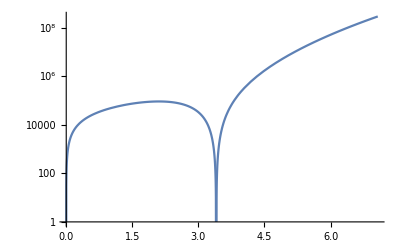

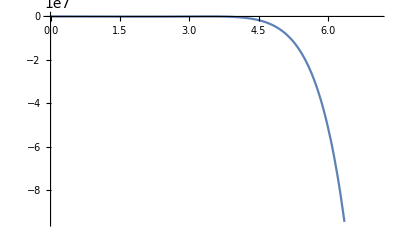

```mathematica
ρrepl ={σc->1,ρM->0.0001,ρω->0.000001,λ0->100,nϕ->4};
Print[(σc/(4 ρM))^(1/4)/.ρrepl]
LogPlot[(z^6 4(ρM/σc -(ρω+λ0 Vϕ[z,(σc/(4 ρM))^(1/4),nϕ])/(2 σc)) - z^2 (1-((ρω+λ0 Vϕ[z,(σc/(4 ρM))^(1/4),nϕ])/σc)^2) + z^10)/.ρrepl,{z,0,(σc/(4 ρM))^(1/4)/.ρrepl}]
Plot[-(z^6 4(ρM/σc -(ρω+λ0 Vϕ[z,(σc/(4 ρM))^(1/4),nϕ])/(2 σc)) - z^2 (1-((ρω+λ0 Vϕ[z,(σc/(4 ρM))^(1/4),nϕ])/σc)^2) + z^10)/.ρrepl,{z,0,(σc/(4 ρM))^(1/4)/.ρrepl}]
```

```mathematica
2.2^4
1.6^4
```

23.4256

6.5536

Is this the right hierarchy?

Metric doesn’t update as we change the energy density of the brane

2.23607

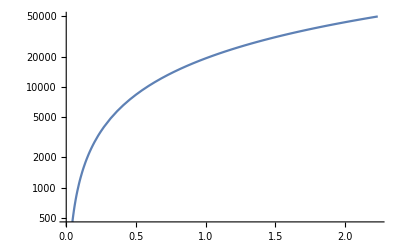

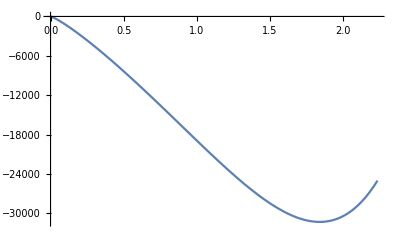

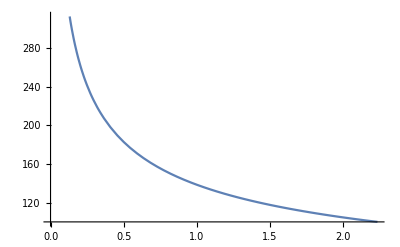

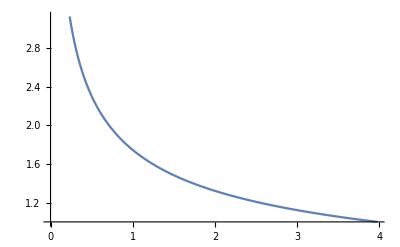

```mathematica
ρrepl ={σc->1,ρM->0.01,ρω->0.001,λ0->10};
Print[(σc/(4 ρM))^(1/4)/.ρrepl]
LogPlot[(z^6 4(ρM/σc -ρω/(2 σc)) - z^2 (1-((ρω+λ0 Vϕ[z,(σc/(4 ρM))^(1/4)])/σc)^2) + z^10(ρω/(ρω+λ0 Vϕ[z,(σc/(4 ρM))^(1/4)]))^2)/.ρrepl,{z,0,(σc/(4 ρM))^(1/4)/.ρrepl}]
Plot[-(z^6 4(ρM/σc -(ρω+λ0 Vϕ[z,(σc/(4 ρM))^(1/4)])/(2 σc)) - z^2 (1-((ρω+λ0 Vϕ[z,(σc/(4 ρM))^(1/4)])/σc)^2) + z^10 ρω^2/((ρω+λ0 Vϕ[z,(σc/(4 ρM))^(1/4)])^2))/.ρrepl,{z,0,(σc/(4 ρM))^(1/4)/.ρrepl}]
Plot[λ0 Vϕ[z,(σc/(4 ρM))^(1/4)]/.ρrepl,{z,0,(σc/(4 ρM))^(1/4)/.ρrepl}]
```

2.23607

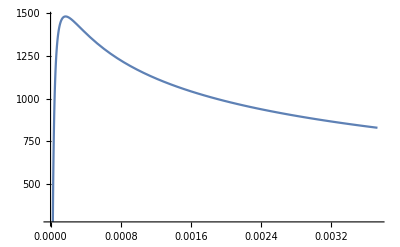

```mathematica
ρrepl ={σc->1,ρM->0.01,ρω->0.001,λ0->10};
Print[(σc/(4 ρM))^(1/4)/.ρrepl]
Plot[10λ0 Vϕ[z,(σc/(4 ρM))^(1/4),4]-λ0 Vϕ[z,(σc/(4 ρM))^(1/4),6]/.ρrepl,{z,0,1/600(σc/(4 ρM))^(1/4)/.ρrepl}]
```

Find extrema of potential

```mathematica
D[-(z^6 4(ρM/σc -(ρω+λ0 VPot[z])/(2 σc)) - z^2 (1-((ρω+λ0 VPot[z])/σc)^2) + z^10),z]/.λ0->0
Solve[%==0,z]
```

-10 z^9+2 z (1-ρω^2/σc^2)-24 z^5 (ρM/σc-ρω/(2 σc))

{{z→0},{z→-((-(6 ρM)/σc+(3 ρω)/σc-(√(36 ρM^2-36 ρM ρω+4 ρω^2+5 σc^2))/σc)^(1/4))/5^(1/4)},{z→-(ⅈ (-(6 ρM)/σc+(3 ρω)/σc-(√(36 ρM^2-36 ρM ρω+4 ρω^2+5 σc^2))/σc)^(1/4))/5^(1/4)},{z→(ⅈ (-(6 ρM)/σc+(3 ρω)/σc-(√(36 ρM^2-36 ρM ρω+4 ρω^2+5 σc^2))/σc)^(1/4))/5^(1/4)},{z→((-(6 ρM)/σc+(3 ρω)/σc-(√(36 ρM^2-36 ρM ρω+4 ρω^2+5 σc^2))/σc)^(1/4))/5^(1/4)},{z→-((-(6 ρM)/σc+(3 ρω)/σc+(√(36 ρM^2-36 ρM ρω+4 ρω^2+5 σc^2))/σc)^(1/4))/5^(1/4)},{z→-(ⅈ (-(6 ρM)/σc+(3 ρω)/σc+(√(36 ρM^2-36 ρM ρω+4 ρω^2+5 σc^2))/σc)^(1/4))/5^(1/4)},{z→(ⅈ (-(6 ρM)/σc+(3 ρω)/σc+(√(36 ρM^2-36 ρM ρω+4 ρω^2+5 σc^2))/σc)^(1/4))/5^(1/4)},{z→((-(6 ρM)/σc+(3 ρω)/σc+(√(36 ρM^2-36 ρM ρω+4 ρω^2+5 σc^2))/σc)^(1/4))/5^(1/4)}}

7.07107

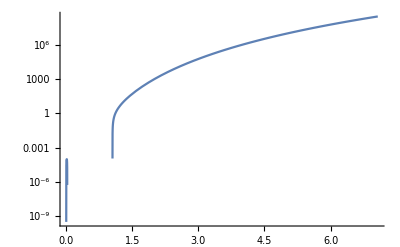

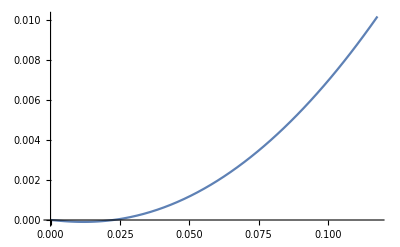

```mathematica
ρrepl ={σc->1,ρM->0.0001,ρω->0.000001,λ0->0.1,nϕ->4};
Print[(σc/(4 ρM))^(1/4)/.ρrepl]
LogPlot[(z^6 4(ρM/σc -(ρω+λ0 Vϕ[z,(σc/(4 ρM))^(1/4),nϕ])/(2 σc)) - z^2 (1-((ρω+λ0 Vϕ[z,(σc/(4 ρM))^(1/4),nϕ])/σc)^2) + z^10)/.ρrepl,{z,0,(σc/(4 ρM))^(1/4)/.ρrepl}]
Plot[-(z^6 4(ρM/σc -(ρω+λ0 Vϕ[z,(σc/(4 ρM))^(1/4),nϕ])/(2 σc)) - z^2 (1-((ρω+λ0 Vϕ[z,(σc/(4 ρM))^(1/4),nϕ])/σc)^2) + z^10)/.ρrepl,{z,0,1/60(σc/(4 ρM))^(1/4)/.ρrepl}]
```

7.07107

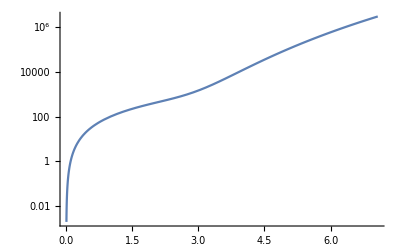

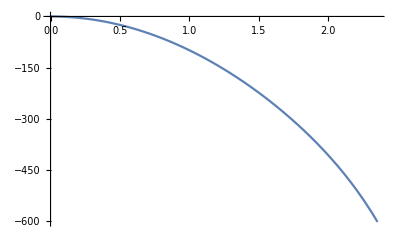

```mathematica
ρrepl ={σc->1,ρM->0.0001,ρω->0.000001,λ0->-10,nϕ->0};
Print[(σc/(4 ρM))^(1/4)/.ρrepl]
LogPlot[(z^6 4(ρM/σc ) - z^2 (1-((ρω+λ0 Vϕ[z,(σc/(4 ρM))^(1/4),nϕ])/σc)^2) + z^10/((ρω+λ0 Vϕ[z,(σc/(4 ρM))^(1/4),nϕ])^2))/.ρrepl,{z,0,(σc/(4 ρM))^(1/4)/.ρrepl}]
Plot[-(z^6 4(ρM/σc ) - z^2 (1-((ρω+λ0 Vϕ[z,(σc/(4 ρM))^(1/4),nϕ])/σc)^2) + z^10/((ρω+λ0 Vϕ[z,(σc/(4 ρM))^(1/4),nϕ])^2))/.ρrepl,{z,0,1/3(σc/(4 ρM))^(1/4)/.ρrepl}]
```

```mathematica
Vϕ
```

```mathematica
Information[Vϕ]
```

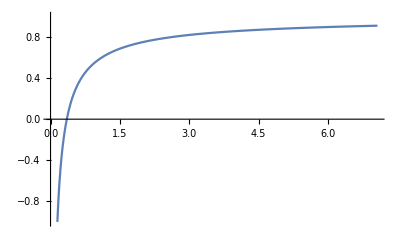

```mathematica
ρrepl ={σc->1,ρM->0.0001,ρω->0.000001,λ0->0.3,nϕ->4};
Plot[1-((ρω-λ0 Vϕ[z,(σc/(4 ρM))^(1/4),nϕ])^2)/σc^2/.ρrepl,{z,0,(σc/(4 ρM))^(1/4)/.ρrepl},PlotRange->{-1,1}]
```

-(4 z^6 ρM)/σc-z^10/((ρω+λ0 LegendreP[0.025,-1+σc/(2 z^4 ρM)]^nϕ)^2)+z^2 (1-((ρω+λ0 LegendreP[0.025,-1+σc/(2 z^4 ρM)]^nϕ)^2)/σc^2)

-(24 z^5 ρM)/σc-(10 z^9)/((ρω+λ0 LegendreP[0.025,-1+σc/(2 z^4 ρM)]^nϕ)^2)+2 z (1-((ρω+λ0 LegendreP[0.025,-1+σc/(2 z^4 ρM)]^nϕ)^2)/σc^2)-(4 nϕ z^5 λ0 σc LegendreP[0.025,-1+σc/(2 z^4 ρM)]^(-1+nϕ) (-1.025 (-1+σc/(2 z^4 ρM)) LegendreP[0.025,-1+σc/(2 z^4 ρM)]+1.025 LegendreP[1.025,-1+σc/(2 z^4 ρM)]))/(ρM (-1+(-1+σc/(2 z^4 ρM))^2) (ρω+λ0 LegendreP[0.025,-1+σc/(2 z^4 ρM)]^nϕ)^3)+(4 nϕ λ0 LegendreP[0.025,-1+σc/(2 z^4 ρM)]^(-1+nϕ) (ρω+λ0 LegendreP[0.025,-1+σc/(2 z^4 ρM)]^nϕ) (-1.025 (-1+σc/(2 z^4 ρM)) LegendreP[0.025,-1+σc/(2 z^4 ρM)]+1.025 LegendreP[1.025,-1+σc/(2 z^4 ρM)]))/(z^3 ρM σc (-1+(-1+σc/(2 z^4 ρM))^2))

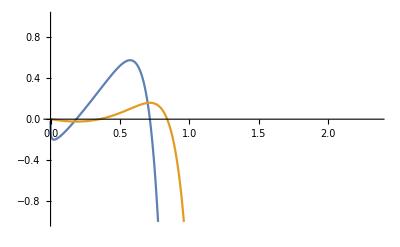

```mathematica
ρrepl ={σc->1,ρM->0.0001,ρω->0.000001,λ0->0.3,nϕ->4};
-(z^6 4(ρM/σc ) - z^2 (1-((ρω+λ0 Vϕ[z,(σc/(4 ρM))^(1/4),nϕ])/σc)^2) + z^10/((ρω+λ0 Vϕ[z,(σc/(4 ρM))^(1/4),nϕ])^2))
D[%,z]
Plot[{%/.ρrepl,%%/.ρrepl},{z,0,1/3(σc/(4 ρM))^(1/4)/.ρrepl},PlotRange->{-1,1}]
```

Try multiple terms in potential

7.07107

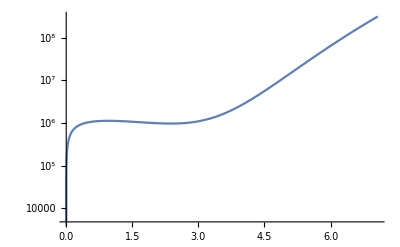

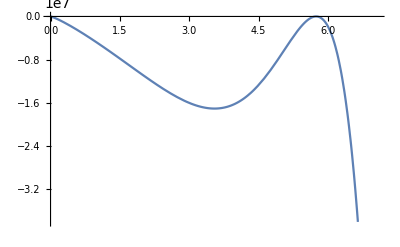

```mathematica
ρrepl ={σc->1,ρM->0.0001,ρω->0.000001,λ0->1000,nϕ->4};
Print[(σc/(4 ρM))^(1/4)/.ρrepl]
LogPlot[(z^6 4(ρM/σc -(ρω+λ0 Vϕ[z,(σc/(4 ρM))^(1/4),nϕ]-λ0 Vϕ[z,(σc/(4 ρM))^(1/4),nϕ+2])/(2 σc)) - z^2 (1-(1/σc(ρω+λ0 Vϕ[z,(σc/(4 ρM))^(1/4),nϕ]-λ0 Vϕ[z,(σc/(4 ρM))^(1/4),nϕ+2]))^2) + z^10)/.ρrepl,{z,0,(σc/(4 ρM))^(1/4)/.ρrepl}]
Plot[-(z^6 4(ρM/σc -(ρω+λ0 Vϕ[z,(σc/(4 ρM))^(1/4),nϕ])/(2 σc)) - z^2 (1-((ρω+λ0 Vϕ[z,(σc/(4 ρM))^(1/4),nϕ])/σc)^2) + z^10)/.ρrepl,{z,0,(σc/(4 ρM))^(1/4)/.ρrepl}]
```

#### plot sigma tilde

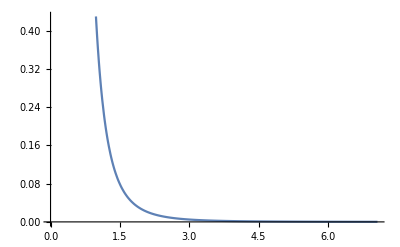

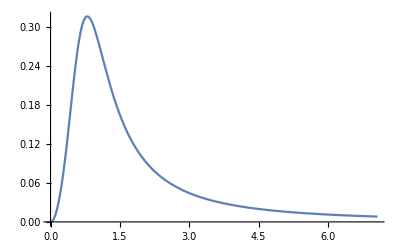

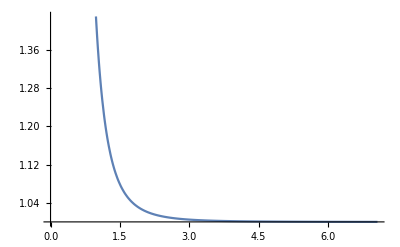

```mathematica
ρrepl ={σc->1,ρM->0.0001,ρω->0.000001,λ0->1000,nϕ->4};
σtilde=1/z D[1/z,z]D[Log[ρω+λ0 Vϕ[z,(σc/(4 ρM))^(1/4),nϕ]],z];
Plot[%/.ρrepl,{z,0,(σc/(4 ρM))^(1/4)/.ρrepl}]
Plot[z^2 σtilde/(σtilde+1)/.ρrepl,{z,0,(σc/(4 ρM))^(1/4)/.ρrepl}]
Plot[σtilde+1/.ρrepl,{z,0,(σc/(4 ρM))^(1/4)/.ρrepl}]
```

### Full Profile

#### Metric and u

```mathematica
Needs["Greater2`"];
```

w::shdw: Symbol w appears in multiple contexts {GREATER2`,Global`}; definitions in context GREATER2` may shadow or be shadowed by other definitions.

z::shdw: Symbol z appears in multiple contexts {GREATER2`,Global`}; definitions in context GREATER2` may shadow or be shadowed by other definitions.

Christoffel::shdw: Symbol Christoffel appears in multiple contexts {GREATER2`,Global`}; definitions in context GREATER2` may shadow or be shadowed by other definitions.

x::shdw: Symbol x appears in multiple contexts {GREATER2`,Global`}; definitions in context GREATER2` may shadow or be shadowed by other definitions.

l::shdw: Symbol l appears in multiple contexts {GREATER2`,Global`}; definitions in context GREATER2` may shadow or be shadowed by other definitions.

m::shdw: Symbol m appears in multiple contexts {GREATER2`,Global`}; definitions in context GREATER2` may shadow or be shadowed by other definitions.

p::shdw: Symbol p appears in multiple contexts {GREATER2`,Global`}; definitions in context GREATER2` may shadow or be shadowed by other definitions.

m$::shdw: Symbol m$ appears in multiple contexts {GREATER2`,Global`}; definitions in context GREATER2` may shadow or be shadowed by other definitions.

X::shdw: Symbol X appears in multiple contexts {GREATER2`,Global`}; definitions in context GREATER2` may shadow or be shadowed by other definitions.

v::shdw: Symbol v appears in multiple contexts {GREATER2`,Global`}; definitions in context GREATER2` may shadow or be shadowed by other definitions.

V::shdw: Symbol V appears in multiple contexts {GREATER2`,Global`}; definitions in context GREATER2` may shadow or be shadowed by other definitions.

g::shdw: Symbol g appears in multiple contexts {GREATER2`,Global`}; definitions in context GREATER2` may shadow or be shadowed by other definitions.

t::shdw: Symbol t appears in multiple contexts {GREATER2`,Global`}; definitions in context GREATER2` may shadow or be shadowed by other definitions.

y::shdw: Symbol y appears in multiple contexts {GREATER2`,Global`}; definitions in context GREATER2` may shadow or be shadowed by other definitions.

GREATER has been loaded. Some functions = antisymmetrize, CoD (covariant derivative), Contract, ds2met (covert line element to metric), Epsilon, KillingEquations, SimpleDeriv (partial derivative), LieD (Lie derivative), ChangeCoords, DAlembertian , FieldStrength (F = dA), IndexShift, symmetrize, TJacobian, Trans2rules, SelfContract, CottonTensor, wedge, ExtrinsicCurvature, ShowComponents

Needs::nocont: Context Greater2` was not created when Needs was evaluated.

```mathematica
Clear[p,u]
gp = {{-g[p],0,0,0,0},{0,p^2/l^2,0,0,0},{0,0,p^2/l^2 r^2,0,0},{0,0,0,p^2/l^2 r^2 Cos[θ]^2,0},{0,0,0,0,1/g[p]}}
X= {t,r,θ,ϕ,p};
(*JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,5}];*)
(*gρ = Simplify[Transpose[JXx].(met5D/.g[z]->1-z^4/zh^4/.z->l^2/ρ/.zh->l^2/ρh).JXx ]*)
gp//MatrixForm 
Simplify[Det[gp]]
Γp=Christoffel[gp, X]
u = {κp[τ]/g[p],r'[τ],0,0,p'[τ]}
```

{{-g[p],0,0,0,0},{0,p^2/l^2,0,0,0},{0,0,(p^2 r^2)/l^2,0,0},{0,0,0,(p^2 r^2 Cos[θ]^2)/l^2,0},{0,0,0,0,1/g[p]}}

(-g[p] | 0 | 0 | 0 | 0
0 | p^2/l^2 | 0 | 0 | 0
0 | 0 | (p^2 r^2)/l^2 | 0 | 0
0 | 0 | 0 | (p^2 r^2 Cos[θ]^2)/l^2 | 0
0 | 0 | 0 | 0 | 1/g[p])

-(p^6 r^4 Cos[θ]^2)/l^6

{{{0,0,0,0,g'[p]/(2 g[p])},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{g'[p]/(2 g[p]),0,0,0,0}},{{0,0,0,0,0},{0,0,0,0,1/p},{0,0,-r,0,0},{0,0,0,-r Cos[θ]^2,0},{0,1/p,0,0,0}},{{0,0,0,0,0},{0,0,1/r,0,0},{0,1/r,0,0,1/p},{0,0,0,Cos[θ] Sin[θ],0},{0,0,1/p,0,0}},{{0,0,0,0,0},{0,0,0,1/r,0},{0,0,0,-Tan[θ],0},{0,1/r,-Tan[θ],0,1/p},{0,0,0,1/p,0}},{{1/2 g[p] g'[p],0,0,0,0},{0,-(p g[p])/l^2,0,0,0},{0,0,-(p r^2 g[p])/l^2,0,0},{0,0,0,-(p r^2 Cos[θ]^2 g[p])/l^2,0},{0,0,0,0,-g'[p]/(2 g[p])}}}

{κp[τ]/g[p],r'[τ],0,0,p'[τ]}

```mathematica
Γp[[5,;;,;;]]
p''[τ]+u.Γp[[5,;;,;;]].u
Simplify[%/.κp->√((1+p^2/l^2 r'[τ]^2)g[p]+p'[τ]^2)]
Γp[[2,;;,;;]]
r''[τ] + u.Γp[[2,;;,;;]].u
```

{{1/2 g[p] g'[p],0,0,0,0},{0,-(p g[p])/l^2,0,0,0},{0,0,-(p r^2 g[p])/l^2,0,0},{0,0,0,-(p r^2 Cos[θ]^2 g[p])/l^2,0},{0,0,0,0,-g'[p]/(2 g[p])}}

(κp^2 g'[p])/(2 g[p])-(g'[p] p'[τ]^2)/(2 g[p])-(p g[p] r'[τ]^2)/l^2+p''[τ]

-(p g[p] r'[τ]^2)/l^2+(g'[p] (l^2+p^2 r'[τ]^2))/(2 l^2)+p''[τ]

{{0,0,0,0,0},{0,0,0,0,1/p},{0,0,-r,0,0},{0,0,0,-r Cos[θ]^2,0},{0,1/p,0,0,0}}

(2 p'[τ] r'[τ])/p+r''[τ]

```mathematica
κr /.κr->(1+p^2/l^2 r'[τ]^2)^(1/2)
Simplify[D[%,p]]
```

√(1+(p^2 r'[τ]^2)/l^2)

(p r'[τ]^2)/(l^2 √(1+(p^2 r'[τ]^2)/l^2))

```mathematica
√((1+p[τ]^2/l^2 r'[τ]^2)g[p[τ]]+p'[τ]^2);
Simplify[D[%,τ]];
√(κr[τ]^2 g[p[τ]]+p'[τ]^2)
Simplify[D[%,τ]]
√(1+p[τ]^2/l^2 r'[τ]^2)
Simplify[D[%,τ]]
```

√(g[p[τ]] κr[τ]^2+p'[τ]^2)

(κr[τ]^2 g'[p[τ]] p'[τ]+2 g[p[τ]] κr[τ] κr'[τ]+2 p'[τ] p''[τ])/(2 √(g[p[τ]] κr[τ]^2+p'[τ]^2))

√(1+(p[τ]^2 r'[τ]^2)/l^2)

(p[τ] r'[τ] (p'[τ] r'[τ]+p[τ] r''[τ]))/(l^2 √(1+(p[τ]^2 r'[τ]^2)/l^2))

```mathematica
√(1+p[τ]^2/l^2 r'[τ]^2)
Simplify[D[%,τ]]
Simplify[1/p'[τ]% +Simplify[D[%%,p[τ]]]]
```

√(1+(p[τ]^2 r'[τ]^2)/l^2)

(p[τ] r'[τ] (p'[τ] r'[τ]+p[τ] r''[τ]))/(l^2 √(1+(p[τ]^2 r'[τ]^2)/l^2))

(p[τ] r'[τ] (2 p'[τ] r'[τ]+p[τ] r''[τ]))/(l^2 p'[τ] √(1+(p[τ]^2 r'[τ]^2)/l^2))

```mathematica
κp/κr/.{κr->(1+p[τ]^2/l^2 r'[τ]^2)^(1/2),κp->√((1+p[τ]^2/l^2 r'[τ]^2)g[p[τ]]+p'[τ]^2)}
Simplify[D[%,τ]]
```

(√(p'[τ]^2+g[p[τ]] (1+(p[τ]^2 r'[τ]^2)/l^2)))/(√(1+(p[τ]^2 r'[τ]^2)/l^2))

(p'[τ] (g'[p[τ]] (l^2+p[τ]^2 r'[τ]^2)^2+2 l^2 (-p[τ] p'[τ]^2 r'[τ]^2+l^2 p''[τ]+p[τ]^2 r'[τ] (r'[τ] p''[τ]-p'[τ] r''[τ]))))/(2 l^2 (l^2+p[τ]^2 r'[τ]^2) √(1+(p[τ]^2 r'[τ]^2)/l^2) √(p'[τ]^2+g[p[τ]] (1+(p[τ]^2 r'[τ]^2)/l^2)))

#### Get expression for K_ττ

```mathematica
ap = Simplify[p''[τ]+u.(Γp[[5,;;,;;]]/.p->p[τ]).u ]
(*Simplify[ap/.κr[τ]->√(1+p[τ]^2/l^2 r'[τ]^2)]*)
ar=r''[τ] + u.(Γp[[2,;;,;;]]/.p->p[τ]).u
κrdτ = Simplify[D[√(1+p[τ]^2/l^2 r'[τ]^2),τ]]
arofκ=Simplify[ar/.Solve[κrdτ==OverDot[κr],r''[τ]]]
κpdτ= D[√(κr[τ]^2 g[p[τ]] + p'[τ]^2),τ]
apofκ=FullSimplify[ap/.Solve[κpdτ==OverDot[κp],p''[τ]]](*/.κr[τ]->√(1/g[p[τ]](κp[τ]^2-p'[τ]^2))]*)
Kττ=FullSimplify[- ap κr/κp+ar/(κp κr)p^2/l^2 r'[τ]p'[τ]]
Kττofκs = FullSimplify[- apofκ κr/κp+arofκ/(κp κr)p[τ]^2/l^2 r'[τ]p'[τ]]
```

(g[p[τ]] κp[τ]^2 g'[p[τ]])/(2 g[p]^2)-(g'[p[τ]] p'[τ]^2)/(2 g[p[τ]])-(g[p[τ]] p[τ] r'[τ]^2)/l^2+p''[τ]

(2 p'[τ] r'[τ])/p[τ]+r''[τ]

(p[τ] r'[τ] (p'[τ] r'[τ]+p[τ] r''[τ]))/(l^2 √(1+(p[τ]^2 r'[τ]^2)/l^2))

{(p[τ] p'[τ] r'[τ]^2+l^2 OverDot[κr] √(1+(p[τ]^2 r'[τ]^2)/l^2))/(p[τ]^2 r'[τ])}

(κr[τ]^2 g'[p[τ]] p'[τ]+2 g[p[τ]] κr[τ] κr'[τ]+2 p'[τ] p''[τ])/(2 √(g[p[τ]] κr[τ]^2+p'[τ]^2))

{1/2 ((g[p[τ]] κp[τ]^2 g'[p[τ]])/g[p]^2-κr[τ]^2 g'[p[τ]]-(g'[p[τ]] p'[τ]^2)/g[p[τ]]+(2 OverDot[κp] √(g[p[τ]] κr[τ]^2+p'[τ]^2))/p'[τ]-(2 g[p[τ]] p[τ] r'[τ]^2)/l^2-(2 g[p[τ]] κr[τ] κr'[τ])/p'[τ])}

(1/2 κr^2 (-(g[p[τ]] κp[τ]^2 g'[p[τ]])/g[p]^2+(g'[p[τ]] p'[τ]^2)/g[p[τ]]+(2 g[p[τ]] p[τ] r'[τ]^2)/l^2-2 p''[τ])+(p^2 p'[τ] r'[τ] ((2 p'[τ] r'[τ])/p[τ]+r''[τ]))/l^2)/(κp κr)

{(-(κr^2 g[p[τ]] κp[τ]^2 g'[p[τ]])/g[p]^2-(2 κr^2 OverDot[κp] √(g[p[τ]] κr[τ]^2+p'[τ]^2))/p'[τ]+(κr^2 g'[p[τ]] (g[p[τ]] κr[τ]^2+p'[τ]^2))/g[p[τ]]+(2 p[τ] (κr^2 g[p[τ]]+p'[τ]^2) r'[τ]^2)/l^2+2 OverDot[κr] p'[τ] √(1+(p[τ]^2 r'[τ]^2)/l^2)+(2 κr^2 g[p[τ]] κr[τ] κr'[τ])/p'[τ])/(2 κp κr)}

```mathematica
Simplify[(-κr[τ])/p'[τ] κp'[τ]+ p'[τ]/(2 κr[τ])κr'[τ] + 1/(2 κr[τ])D[κr[τ]^2, p] + g[p[τ]]/2 κr/p'[τ] D[κr[τ]^2, τ]/κp[τ]]
```

(p'[τ] κr'[τ])/(2 κr[τ])+(κr[τ] (-κp[τ] κp'[τ]+κr g[p[τ]] κr'[τ]))/(κp[τ] p'[τ])

```mathematica
Simplify[-(κr OverDot[κp] κp)/(κp p'[τ])+((p[τ] κp^2 r'[τ]^2)/l^2+OverDot[κr] p'[τ] κr+(κr^2 g[p[τ]] κr[τ] κr'[τ])/p'[τ])/(κp κr)]
Simplify[%]
```

-(κr OverDot[κp])/p'[τ]+(OverDot[κr] p'[τ]+(κp^2 p[τ] r'[τ]^2)/(l^2 κr)+(κr g[p[τ]] κr[τ] κr'[τ])/p'[τ])/κp

-(κr OverDot[κp])/p'[τ]+(OverDot[κr] p'[τ]+(κp^2 p[τ] r'[τ]^2)/(l^2 κr)+(κr g[p[τ]] κr[τ] κr'[τ])/p'[τ])/κp

```mathematica
Simplify[-(κr OverDot[κp] κp)/(κp p'[τ])+((p[τ] κp r'[τ]^2)/l^2+OverDot[κr] p'[τ] κr+(κr^2 g[p[τ]] κr[τ] κr'[τ])/p'[τ])/(κp κr)]
```

-(κr OverDot[κp])/p'[τ]+(OverDot[κr] p'[τ])/κp+(p[τ] r'[τ]^2)/(l^2 κr)+(κr g[p[τ]] κr[τ] κr'[τ])/(κp p'[τ])

```mathematica
Simplify[(-κr[τ])/p'[τ] κp'[τ]+ p'[τ]/(2 κr[τ])κr'[τ] + 1/(2 κr[τ])D[κr[τ]^2, p] + g[p[τ]]/2 κr/p'[τ] D[κ[τ]^2, τ]/κp[τ]]
```

((2 κr g[p[τ]] κ[τ] κ'[τ])/κp[τ]-2 κr[τ] κp'[τ]+(p'[τ]^2 κr'[τ])/κr[τ])/(2 p'[τ])

```mathematica
Γp[[1,;;,;;]]
```

{{0,0,0,0,g'[p]/(2 g[p])},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{g'[p]/(2 g[p]),0,0,0,0}}

```mathematica
Simplify[D[1+p[τ]^2/l^2 r'[τ]^2,τ]+κp/p'[τ] D[1+p[τ]^2/l^2 r'[τ]^2,p[τ]]]
```

(2 p[τ] r'[τ] ((κp+p'[τ]^2) r'[τ]+p[τ] p'[τ] r''[τ]))/(l^2 p'[τ])

```mathematica
FullSimplify[√(κr[τ]^2 g[p[τ]] + p'[τ]^2)Simplify[D[√(1+p[τ]^2/l^2 r'[τ]^2),τ]]-√(1+p[τ]^2/l^2 r'[τ]^2)D[√(κr[τ]^2 g[p[τ]] + p'[τ]^2),τ]]
```

(-((l^2+p[τ]^2 r'[τ]^2) (κr[τ]^2 g'[p[τ]] p'[τ]+2 g[p[τ]] κr[τ] κr'[τ]+2 p'[τ] p''[τ]))+2 p[τ] (g[p[τ]] κr[τ]^2+p'[τ]^2) r'[τ] (p'[τ] r'[τ]+p[τ] r''[τ]))/(2 l^2 √(g[p[τ]] κr[τ]^2+p'[τ]^2) √(1+(p[τ]^2 r'[τ]^2)/l^2))

#### Get expression for K_ττ - uncorrected

```mathematica
ap = Simplify[p''[τ]+u.(Γp[[5,;;,;;]]).u ]/.κp[τ]->√(κr^2 g[p]+p'[τ]^2)
(*Simplify[ap/.κr[τ]->√(1+p[τ]^2/l^2 r'[τ]^2)]*)
ar=r''[τ] + u.(Γp[[2,;;,;;]]).u
```

1/2 κr^2 g'[p]-(p g[p] r'[τ]^2)/l^2+p''[τ]

(2 p'[τ] r'[τ])/p+r''[τ]

```mathematica
κrdτ = Simplify[D[√(1+p[τ]^2/l^2 r'[τ]^2),τ]]
(*κrdτ =(p[τ]^2 r'[τ] r''[τ])/(l^2 κr)*)
κrdτ = Simplify[(p[τ] r'[τ] (p'[τ] r'[τ]+p[τ] r''[τ]))/(l^2 κr)]
```

(p[τ] r'[τ] (p'[τ] r'[τ]+p[τ] r''[τ]))/(l^2 √(1+(p[τ]^2 r'[τ]^2)/l^2))

(p[τ] r'[τ] (p'[τ] r'[τ]+p[τ] r''[τ]))/(l^2 κr)

```mathematica
κpdτ= D[√(κr[τ]^2 g[p[τ]] + p'[τ]^2),τ]
(*κpdτ=Simplify[(2 g[p] κr OverDot[κr]+2 p'[τ] p''[τ])/(2 κp)]*)
κpdτ=Simplify[(κr^2 g'[p[τ]] p'[τ]+2 g[p[τ]] κr OverDot[κr]+2 p'[τ] p''[τ])/(2 κp)]
```

(κr[τ]^2 g'[p[τ]] p'[τ]+2 g[p[τ]] κr[τ] κr'[τ]+2 p'[τ] p''[τ])/(2 √(g[p[τ]] κr[τ]^2+p'[τ]^2))

(2 κr g[p[τ]] OverDot[κr]+p'[τ] (κr^2 g'[p[τ]]+2 p''[τ]))/(2 κp)

```mathematica
arofκ=Simplify[ar/.Solve[κrdτ==OverDot[κr],r''[τ]][[1]]]
arofκ = (l^2 κr OverDot[κr])/(p[τ]^2 r'[τ])+(p'[τ] r'[τ])/p[τ]
```

(l^2 κr OverDot[κr])/(p[τ]^2 r'[τ])-((p-2 p[τ]) p'[τ] r'[τ])/(p p[τ])

(l^2 κr OverDot[κr])/(p[τ]^2 r'[τ])+(p'[τ] r'[τ])/p[τ]

```mathematica
apofκ=FullSimplify[ap/.Solve[κpdτ==OverDot[κp],p''[τ]][[1]]]
apofκ =Simplify[(κp OverDot[κp]-κr g[p[τ]] OverDot[κr])/p'[τ]-(p[τ] g[p[τ]] r'[τ]^2)/l^2]
```

1/2 κr^2 g'[p]-1/2 κr^2 g'[p[τ]]+(κp OverDot[κp]-κr g[p[τ]] OverDot[κr])/p'[τ]-(p g[p] r'[τ]^2)/l^2

(κp OverDot[κp]-κr g[p[τ]] OverDot[κr])/p'[τ]-(g[p[τ]] p[τ] r'[τ]^2)/l^2

```mathematica
(*/.κr[τ]->√(1/g[p[τ]](κp[τ]^2-p'[τ]^2))]*)
Kττ=FullSimplify[- ap κr/κp+ar/(κp κr)p^2/l^2 r'[τ]p'[τ]]
```

(κr^2 (-1/2 κr^2 g'[p]+(p g[p] r'[τ]^2)/l^2-p''[τ])+(p p'[τ] r'[τ] (2 p'[τ] r'[τ]+p r''[τ]))/l^2)/(κp κr)

```mathematica
Kττofκs = FullSimplify[- apofκ κr/κp+arofκ/(κp κr)p^2/l^2 r'[τ]p'[τ]]
(-κr^2 OverDot[κp]+(κp (l^2 κr OverDot[κr]+p[τ] p'[τ] r'[τ]^2))/l^2)/(κr p'[τ])
```

(-κr^2 OverDot[κp]+((κr^2 g[p[τ]] p[τ]^2+p^2 p'[τ]^2) (l^2 κr OverDot[κr]+p[τ] p'[τ] r'[τ]^2))/(l^2 κp p[τ]^2))/(κr p'[τ])

(-κr^2 OverDot[κp]+(κp (l^2 κr OverDot[κr]+p[τ] p'[τ] r'[τ]^2))/l^2)/(κr p'[τ])

```mathematica
Expand[Kττofκs ]
Expand[Simplify[%/.κp[τ]->√(g[p] κr^2 + p'[τ]^2)]]
Expand[Simplify[%/.  (κr^2 g[p] OverDot[κr])/(κp p'[τ])+(OverDot[κr] p'[τ])/κp->(OverDot[κr] κp)/p'[τ]]]
(*Expand[Simplify[%/. 2 (p r'[τ]^2)/(l^2 κr)->2dpκr]]
Expand[Simplify[%/.  (κr p r'[τ]^2)/l^2->2 κr dpκr2]]*)
```

-(κr^3 g'[p])/(2 κp)-(κr OverDot[κp])/p'[τ]+(κr^2 g[p] OverDot[κr])/(κp p'[τ])+(OverDot[κr] p'[τ])/κp+(p κr g[p] r'[τ]^2)/(l^2 κp)+(2 p p'[τ]^2 r'[τ]^2)/(l^2 κp κr)

-(κr^3 g'[p])/(2 κp)-(κr OverDot[κp])/p'[τ]+(κr^2 g[p] OverDot[κr])/(κp p'[τ])+(OverDot[κr] p'[τ])/κp+(p κr g[p] r'[τ]^2)/(l^2 κp)+(2 p p'[τ]^2 r'[τ]^2)/(l^2 κp κr)

-(κr^3 g'[p])/(2 κp)-(κr OverDot[κp])/p'[τ]+(κp OverDot[κr])/p'[τ]+(p κr g[p] r'[τ]^2)/(l^2 κp)+(2 p p'[τ]^2 r'[τ]^2)/(l^2 κp κr)

```mathematica
Simplify[(2 dpκr2 κr g[p])/κp-(κr^3 g'[p])/(2 κp)-(κr OverDot[κp])/p'[τ]+(κp OverDot[κr])/p'[τ]+(2 dpκr p'[τ]^2)/κp/. { dpκr->(p r'[τ]^2)/(l^2 κr),dpκr2->(p r'[τ]^2)/l^2}]
```

-(κr^3 g'[p])/(2 κp)-(κr OverDot[κp])/p'[τ]+(κp OverDot[κr])/p'[τ]+(2 p (κr^2 g[p]+p'[τ]^2) r'[τ]^2)/(l^2 κp κr)

```mathematica
Simplify[D[√(1+p^2/l^2 r'[τ]^2),p]]
Simplify[D[1+p^2/l^2 r'[τ]^2,p]]
```

(p r'[τ]^2)/(l^2 √(1+(p^2 r'[τ]^2)/l^2))

(2 p r'[τ]^2)/l^2

#### Solve EOM for z

```mathematica
DSolve[z'[τ]^2== z[τ]^6 HM^2-z[τ]^2 H^2+z[τ]^10,z[τ],τ]
PowerExpand[%]
D[%,τ]
D[%,τ]
```

{{z[τ]→InverseFunction[-(ArcTan[(#1^4-√(-H^2+HM^2 #1^4+#1^8))/H] #1 √(-H^2+HM^2 #1^4+#1^8))/(2 H √(#1^2 (-H^2+HM^2 #1^4+#1^8)))&][-τ+C[1]]},{z[τ]→InverseFunction[-(ArcTan[(#1^4-√(-H^2+HM^2 #1^4+#1^8))/H] #1 √(-H^2+HM^2 #1^4+#1^8))/(2 H √(#1^2 (-H^2+HM^2 #1^4+#1^8)))&][τ+C[1]]}}

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

{{z[τ]→-(H^(1/4) (1+Tan[2 H (-τ+C[1])]^2)^(1/4))/((HM^2/H-2 Tan[2 H (-τ+C[1])])^(1/4))},{z[τ]→-(H^(1/4) (1+Tan[2 H (τ+C[1])]^2)^(1/4))/((HM^2/H-2 Tan[2 H (τ+C[1])])^(1/4))}}

{{z'[τ]→(H^(5/4) Sec[2 H (-τ+C[1])]^2 Tan[2 H (-τ+C[1])])/((HM^2/H-2 Tan[2 H (-τ+C[1])])^(1/4) (1+Tan[2 H (-τ+C[1])]^2)^(3/4))+(H^(5/4) Sec[2 H (-τ+C[1])]^2 (1+Tan[2 H (-τ+C[1])]^2)^(1/4))/((HM^2/H-2 Tan[2 H (-τ+C[1])])^(5/4))},{z'[τ]→-(H^(5/4) Sec[2 H (τ+C[1])]^2 Tan[2 H (τ+C[1])])/((HM^2/H-2 Tan[2 H (τ+C[1])])^(1/4) (1+Tan[2 H (τ+C[1])]^2)^(3/4))-(H^(5/4) Sec[2 H (τ+C[1])]^2 (1+Tan[2 H (τ+C[1])]^2)^(1/4))/((HM^2/H-2 Tan[2 H (τ+C[1])])^(5/4))}}

{{z''[τ]→(3 H^(9/4) Sec[2 H (-τ+C[1])]^4 Tan[2 H (-τ+C[1])]^2)/((HM^2/H-2 Tan[2 H (-τ+C[1])])^(1/4) (1+Tan[2 H (-τ+C[1])]^2)^(7/4))-(2 H^(9/4) Sec[2 H (-τ+C[1])]^4)/((HM^2/H-2 Tan[2 H (-τ+C[1])])^(1/4) (1+Tan[2 H (-τ+C[1])]^2)^(3/4))-(2 H^(9/4) Sec[2 H (-τ+C[1])]^4 Tan[2 H (-τ+C[1])])/((HM^2/H-2 Tan[2 H (-τ+C[1])])^(5/4) (1+Tan[2 H (-τ+C[1])]^2)^(3/4))-(4 H^(9/4) Sec[2 H (-τ+C[1])]^2 Tan[2 H (-τ+C[1])]^2)/((HM^2/H-2 Tan[2 H (-τ+C[1])])^(1/4) (1+Tan[2 H (-τ+C[1])]^2)^(3/4))-(5 H^(9/4) Sec[2 H (-τ+C[1])]^4 (1+Tan[2 H (-τ+C[1])]^2)^(1/4))/((HM^2/H-2 Tan[2 H (-τ+C[1])])^(9/4))-(4 H^(9/4) Sec[2 H (-τ+C[1])]^2 Tan[2 H (-τ+C[1])] (1+Tan[2 H (-τ+C[1])]^2)^(1/4))/((HM^2/H-2 Tan[2 H (-τ+C[1])])^(5/4))},{z''[τ]→(3 H^(9/4) Sec[2 H (τ+C[1])]^4 Tan[2 H (τ+C[1])]^2)/((HM^2/H-2 Tan[2 H (τ+C[1])])^(1/4) (1+Tan[2 H (τ+C[1])]^2)^(7/4))-(2 H^(9/4) Sec[2 H (τ+C[1])]^4)/((HM^2/H-2 Tan[2 H (τ+C[1])])^(1/4) (1+Tan[2 H (τ+C[1])]^2)^(3/4))-(2 H^(9/4) Sec[2 H (τ+C[1])]^4 Tan[2 H (τ+C[1])])/((HM^2/H-2 Tan[2 H (τ+C[1])])^(5/4) (1+Tan[2 H (τ+C[1])]^2)^(3/4))-(4 H^(9/4) Sec[2 H (τ+C[1])]^2 Tan[2 H (τ+C[1])]^2)/((HM^2/H-2 Tan[2 H (τ+C[1])])^(1/4) (1+Tan[2 H (τ+C[1])]^2)^(3/4))-(5 H^(9/4) Sec[2 H (τ+C[1])]^4 (1+Tan[2 H (τ+C[1])]^2)^(1/4))/((HM^2/H-2 Tan[2 H (τ+C[1])])^(9/4))-(4 H^(9/4) Sec[2 H (τ+C[1])]^2 Tan[2 H (τ+C[1])] (1+Tan[2 H (τ+C[1])]^2)^(1/4))/((HM^2/H-2 Tan[2 H (τ+C[1])])^(5/4))}}

So we want H -> 0 at the extremum.

```mathematica
Solve[σc^2 == (ρ-λ0 ϕ^4 l^2)^2,ϕ]
Solve[(ϕos1type3/.z->zh y^(-1/4))==a,y]
```

{{ϕ→-(ρ-σc)^(1/4)/(√l λ0^(1/4))},{ϕ→-(ⅈ (ρ-σc)^(1/4))/(√l λ0^(1/4))},{ϕ→(ⅈ (ρ-σc)^(1/4))/(√l λ0^(1/4))},{ϕ→(ρ-σc)^(1/4)/(√l λ0^(1/4))},{ϕ→-(ρ+σc)^(1/4)/(√l λ0^(1/4))},{ϕ→-(ⅈ (ρ+σc)^(1/4))/(√l λ0^(1/4))},{ϕ→(ⅈ (ρ+σc)^(1/4))/(√l λ0^(1/4))},{ϕ→(ρ+σc)^(1/4)/(√l λ0^(1/4))}}

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[LegendreP[ϵ/4,-1+2 y]==a,y]

```mathematica
ftemp[z_]:=ϕos1type3
InverseFunction[ftemp[z]]
```

InverseFunction[LegendreP[ϵ/4,-1+(2 zh^4)/z^4]][1]

#### Conservation of T

```mathematica
gpinducedupup = Inverse[gp] - DiagonalMatrix[{0,0,0,0,gp[[5,5]]^-1}]
TBulk =PowerExpand[FullSimplify[ 1/(√gp[[5,5]]) DiracDelta[p-p0]σ[τ,r,p] gpinducedupup]]
Table[D[TBulk[[;;,i]],X[[i]]],{i,5}]
```

{{-1/g[p],0,0,0,0},{0,l^2/p^2,0,0,0},{0,0,l^2/(p^2 r^2),0,0},{0,0,0,(l^2 Sec[θ]^2)/(p^2 r^2),0},{0,0,0,0,0}}

{{-(DiracDelta[p-p0] σ[τ,r,p])/(√g[p]),0,0,0,0},{0,(l^2 DiracDelta[p-p0] √g[p] σ[τ,r,p])/p^2,0,0,0},{0,0,(l^2 DiracDelta[p-p0] √g[p] σ[τ,r,p])/(p^2 r^2),0,0},{0,0,0,(l^2 DiracDelta[p-p0] √g[p] Sec[θ]^2 σ[τ,r,p])/(p^2 r^2),0},{0,0,0,0,0}}

{{0,0,0,0,0},{0,(l^2 DiracDelta[p-p0] √g[p] σ^(0,1,0)[τ,r,p])/p^2,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}

```mathematica
FullSimplify[Table[Sum[Γp[[i,j,k]]TBulk[[j,k]]+Γp[[j,j,k]]TBulk[[i,k]],{j,5},{k,5}],{i,5}]]
```

{0,0,0,0,-(3 DiracDelta[p-p0] g[p]^(3/2) σ[τ,r,p])/p-1/2 DiracDelta[p-p0] √g[p] σ[τ,r,p] g'[p]}

so for r independent σ, it is only this last term that needs to vanish for T to be conserved.

#### R eom (w rdot=0)

```mathematica
Simplify[Solve[√(gp[p]+ pd^2)-√(gm[p]+ pd^2)==p 2/l σ/σc,pd]]
FullSimplify[Solve[√(gp[p]+ pds)-√(gm[p]+ pds)==p a,pds]]
FullSimplify[%/.{gm[p]->p^2/l^2-2 μm/p^2,gp[p]->p^2/l^2-2 μp/p^2,a->-2/l σ/σc}]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{pd→-(√(l^4 σc^4 gm[p]^2+(-4 p^2 σ^2+l^2 σc^2 gp[p])^2-2 gm[p] (4 l^2 p^2 σ^2 σc^2+l^4 σc^4 gp[p])))/(4 l p σ σc)},{pd→(√(l^4 σc^4 gm[p]^2+(-4 p^2 σ^2+l^2 σc^2 gp[p])^2-2 gm[p] (4 l^2 p^2 σ^2 σc^2+l^4 σc^4 gp[p])))/(4 l p σ σc)}}

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{pds→(gm[p]^2+(-a^2 p^2+gp[p])^2-2 gm[p] (a^2 p^2+gp[p]))/(4 a^2 p^2)}}

{{pds→(μm+μp)/p^2+(l^2 (μm-μp)^2 σc^2)/(4 p^6 σ^2)+(p^2 (σ-σc) (σ+σc))/(l^2 σc^2)}}

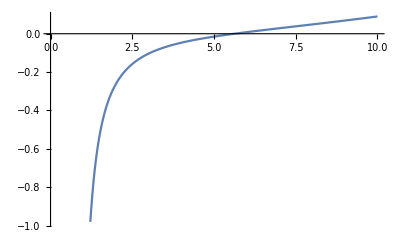

```mathematica
Plot[-(HM/p^2-H p^2+a/p^6)/.{HM->1,H->10^-3,a->1},{p,0,10}]
```

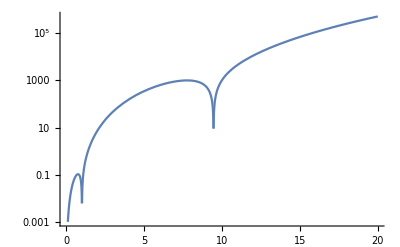

```mathematica
LogPlot[Abs[z^3-z^4+0.01 z^6],{z,0,20}]
```

#### Potential of the brane - conformal potential

Conformal implies that whatever potential is on the brane has to scale as 1/z^4

7.07107

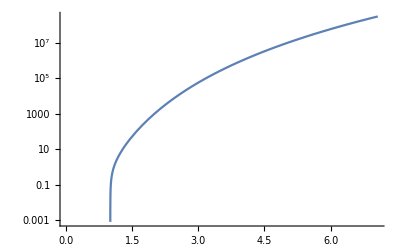

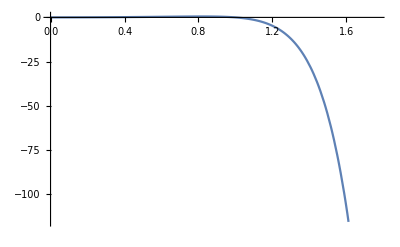

```mathematica
ρrepl ={σc->1,ρM->0.0001,ρω->0.000001,λ0->0,nϕ->4};
Print[(σc/(4 ρM))^(1/4)/.ρrepl]
LogPlot[(z^6 4(ρM/σc -(ρω+λ0 z^-4)/(2 σc)) - z^2 (1-((ρω+λ0 z^-4)/σc)^2) + z^10)/.ρrepl,{z,0,(σc/(4 ρM))^(1/4)/.ρrepl}]
Plot[-(z^6 4(ρM/σc -(ρω+λ0 z^-4)/(2 σc)) - z^2 (1-((ρω + λ0 z^-4)/σc)^2) + z^10)/.ρrepl,{z,0,1/4(σc/(4 ρM))^(1/4)/.ρrepl}]
```

```mathematica
ϕos1type3/.ϵ->-100.1
```

LegendreP[-25.025,-1+(2 zh^4)/z^4]

```mathematica
ϕΔ=Integrate[(z/(z^2+(x-y)^2))^2 vUV^2,y]
Limit[%,y->∞]
Limit[%,y->-∞]
```

-(vUV^2 (((x-y) z)/((x-y)^2+z^2)+ArcTan[(x-y)/z]))/(2 z)

1/4 π vUV^2 √(1/z^2)

1/4 π vUV^2 √(1/z^2)

```mathematica
ϕΔ=Integrate[y^3(z/(z^2+(x-y)^2))^2 vUV^2,y]
Simplify[(%/.y->a)-(%/.y->-a)]
Limit[%,a->∞]
```

1/2 vUV^2 z^2 ((-x^4+x^3 y-3 x y z^2+z^4)/(z^2 (x^2-2 x y+y^2+z^2))-((x^3+3 x z^2) ArcTan[(x-y)/z])/z^3+Log[(x-y)^2+z^2])

1/2 vUV^2 z^2 ((x^4-z^4+a (x^3-3 x z^2))/(z^2 (a^2+2 a x+x^2+z^2))+(-x^4+z^4+a (x^3-3 x z^2))/(z^2 (a^2-2 a x+x^2+z^2))+((x^3+3 x z^2) ArcTan[(a-x)/z])/z^3+((x^3+3 x z^2) ArcTan[(a+x)/z])/z^3+Log[(a-x)^2+z^2]-Log[(a+x)^2+z^2])

1/2 π vUV^2 x √(1/z^2) (x^2+3 z^2)

#### Solve for metric on either side of the brane at the horizon

```mathematica
Solve[0 == z^6 4/σc(ρM - ρ/2) - z^2 (1-ρ^2/σc^2) + z^10,z]
```

{{z→0},{z→0},{z→-(ρ/σc-(2 ρM)/σc-(√(-4 ρ ρM+4 ρM^2+σc^2))/σc)^(1/4)},{z→-ⅈ (ρ/σc-(2 ρM)/σc-(√(-4 ρ ρM+4 ρM^2+σc^2))/σc)^(1/4)},{z→ⅈ (ρ/σc-(2 ρM)/σc-(√(-4 ρ ρM+4 ρM^2+σc^2))/σc)^(1/4)},{z→(ρ/σc-(2 ρM)/σc-(√(-4 ρ ρM+4 ρM^2+σc^2))/σc)^(1/4)},{z→-(ρ/σc-(2 ρM)/σc+(√(-4 ρ ρM+4 ρM^2+σc^2))/σc)^(1/4)},{z→-ⅈ (ρ/σc-(2 ρM)/σc+(√(-4 ρ ρM+4 ρM^2+σc^2))/σc)^(1/4)},{z→ⅈ (ρ/σc-(2 ρM)/σc+(√(-4 ρ ρM+4 ρM^2+σc^2))/σc)^(1/4)},{z→(ρ/σc-(2 ρM)/σc+(√(-4 ρ ρM+4 ρM^2+σc^2))/σc)^(1/4)}}

```mathematica
Solve[0 == z^6 4/σc(ρM - ρ/2) - z^2 (1-ρ^2/σc^2) + z^10,z]
```

```mathematica
Solve[ -(1-zhp^4/zhm^4)^(1/2)==2/z σ/σc,zhm]/.z->zhm
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{zhm→-(√zhm zhp √σc)/((-4 σ^2+zhm^2 σc^2)^(1/4))},{zhm→-(ⅈ √zhm zhp √σc)/((-4 σ^2+zhm^2 σc^2)^(1/4))},{zhm→(ⅈ √zhm zhp √σc)/((-4 σ^2+zhm^2 σc^2)^(1/4))},{zhm→(√zhm zhp √σc)/((-4 σ^2+zhm^2 σc^2)^(1/4))}}

#### plot sigma tilde

```mathematica
ρrepl ={σc->1,ρM->0.0001,ρω->0.000001,λ0->1000,nϕ->4};
σtilde=1/z D[1/z,z]D[Log[ρω+λ0 Vϕ[z,(σc/(4 ρM))^(1/4),nϕ]],z];
Plot[%/.ρrepl,{z,0,(σc/(4 ρM))^(1/4)/.ρrepl}]
Plot[z^2 σtilde/(σtilde+1)/.ρrepl,{z,0,(σc/(4 ρM))^(1/4)/.ρrepl}]
Plot[σtilde+1/.ρrepl,{z,0,(σc/(4 ρM))^(1/4)/.ρrepl}]
```

-Graphics-

-Graphics-

-Graphics-

#### Global time potential

-(4 z^6 ρM)/σc-z^10/((ρω+λ0 LegendreP[0.025,-1+σc/(2 z^4 ρM)]^nϕ)^2)+z^2 (1-((ρω+λ0 LegendreP[0.025,-1+σc/(2 z^4 ρM)]^nϕ)^2)/σc^2)

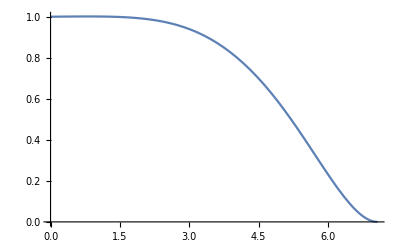

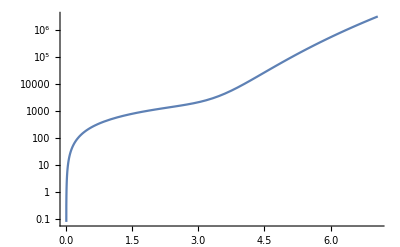

```mathematica
ρrepl ={σc->1,ρM->0.0001,ρω->0.000001,λ0->-10,nϕ->4};
zd2=-(z^6 4(ρM/σc ) - z^2 (1-((ρω+λ0 Vϕ[z,(σc/(4 ρM))^(1/4),nϕ])/σc)^2) + z^10/((ρω+λ0 Vϕ[z,(σc/(4 ρM))^(1/4),nϕ])^2))
(*Show[{Plot[(1-z^4(σc/(4 ρM))^-1)^2 zd2/(z^2(1-z^4(σc/(4 ρM))^-1)^2+zd2)/.ρrepl,{z,0,(σc/(4 ρM))^(1/4)/.ρrepl}],Plot[zd2/.ρrepl,{z,0,(σc/(4 ρM))^(1/4)/.ρrepl}]}]*)
Plot[(1-z^4(σc/(4 ρM))^-1)^2 zd2/(z^2(1-z^4(σc/(4 ρM))^-1)^2+zd2)/.ρrepl,{z,0,(σc/(4 ρM))^(1/4)/.ρrepl}]
LogPlot[-zd2/.ρrepl,{z,0,(σc/(4 ρM))^(1/4)/.ρrepl}]
(*Plot[(1-z^4(σc/(4 ρM)))^2 zd2/(z^2(1-(σc/(4 ρM)))^2+zd2)/.ρrepl,{z,0,1/40(σc/(4 ρM))^(1/4)/.ρrepl}]*)
```

#### Energy momentum tensor

```mathematica
Γp
```

{{{0,0,0,0,g'[p]/(2 g[p])},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{g'[p]/(2 g[p]),0,0,0,0}},{{0,0,0,0,0},{0,0,0,0,1/p},{0,0,-r,0,0},{0,0,0,-r Cos[θ]^2,0},{0,1/p,0,0,0}},{{0,0,0,0,0},{0,0,1/r,0,0},{0,1/r,0,0,1/p},{0,0,0,Cos[θ] Sin[θ],0},{0,0,1/p,0,0}},{{0,0,0,0,0},{0,0,0,1/r,0},{0,0,0,-Tan[θ],0},{0,1/r,-Tan[θ],0,1/p},{0,0,0,1/p,0}},{{1/2 g[p] g'[p],0,0,0,0},{0,-(p g[p])/l^2,0,0,0},{0,0,-(p r^2 g[p])/l^2,0,0},{0,0,0,-(p r^2 Cos[θ]^2 g[p])/l^2,0},{0,0,0,0,-g'[p]/(2 g[p])}}}

```mathematica
D[σ[p]gp,p] - σ[p]Γp[[5,;;,;;]].gp
```

{{-σ[p] g'[p]+1/2 g[p]^2 σ[p] g'[p]-g[p] σ'[p],0,0,0,0},{0,(2 p σ[p])/l^2+(p^3 g[p] σ[p])/l^4+(p^2 σ'[p])/l^2,0,0,0},{0,0,(2 p r^2 σ[p])/l^2+(p^3 r^4 g[p] σ[p])/l^4+(p^2 r^2 σ'[p])/l^2,0,0},{0,0,0,(2 p r^2 Cos[θ]^2 σ[p])/l^2+(p^3 r^4 Cos[θ]^4 g[p] σ[p])/l^4+(p^2 r^2 Cos[θ]^2 σ'[p])/l^2,0},{0,0,0,0,-(σ[p] g'[p])/(2 g[p]^2)+σ'[p]/g[p]}}

#### Expand GW around z->0

```mathematica
ϕos1type3 = PowerExpand[Simplify[LegendreP[1/4 (-2+√(4+l^2 m^2)),0,3,-1+2 y]/.m->(√(ϵ(4+ϵ)))/l]]/.y->(zh/z)^4
ϕos2type3 =PowerExpand[Simplify[LegendreQ[1/4 (-2+√(4+l^2 m^2)),0,3,-1+2 y]/.m->(√(ϵ(4+ϵ)))/l]]/.y->(zh/z)^4
Vϕ[zt_,zht_,n_,ϵt_:0.1]:=ϕos1type3^n/.{zh->zht,z->zt,ϵ->ϵt}
```

LegendreP[ϵ/4,-1+(2 zh^4)/z^4]

LegendreQ[ϵ/4,0,3,-1+(2 zh^4)/z^4]

Near ads boundary we have at next to leading order

```mathematica
dz2 ==Series[ z^2 (σ^2/σc^2-1)/.σ->Vϕ[z,zh,n,ϵ],{z,0,1}]
```

dz2==(1+LegendreP[ϵ/4,-1+(2 zh^4)/z^4]^(2 n)) O[z]^2

```mathematica
PowerExpand[Series[ϕos1type3,{z,0,4}]]
Simplify[PowerExpand[Expand[Normal[%]]]]
Series[Normal[%],{ϵ,0,2}]
```

z^ϵ zh^-ϵ (((Gamma[-1-ϵ/2] z^4)/(zh^4 Gamma[-ϵ/4]^2)+O[z]^5)+z^(-2 ϵ) ((zh^(2 ϵ) Gamma[1+ϵ/2])/Gamma[1+ϵ/4]^2-((zh^(4 (-1+ϵ/2)) ϵ Gamma[1+ϵ/2]) z^4)/(8 Gamma[1+ϵ/4]^2)+O[z]^5))

(z^-ϵ zh^(-4+ϵ) (8 zh^4-z^4 ϵ) Gamma[1+ϵ/2])/(8 Gamma[1+ϵ/4]^2)+(z^(4+ϵ) zh^(-4-ϵ) Gamma[-1-ϵ/2])/Gamma[-ϵ/4]^2

1+(-Log[z]+Log[zh]) ϵ+((-6 z^4+π^2 zh^4+24 z^4 Log[z]+48 zh^4 Log[z]^2-24 z^4 Log[zh]-96 zh^4 Log[z] Log[zh]+48 zh^4 Log[zh]^2) ϵ^2)/(96 zh^4)+O[ϵ]^3

```mathematica
PowerExpand[Series[ϕos1type3,{z,zh,1}]]
```

1-((ϵ (4+ϵ)) (z-zh))/(4 zh)+O[z-zh]^2

```mathematica
Series[Gamma[1+ϵ/2]/Gamma[1+ϵ/4]^2,{ϵ,0,2}]
```

1+(π^2 ϵ^2)/96+O[ϵ]^3

```mathematica
ϕboundary = Gamma[1+ϵ/2]/Gamma[1+ϵ/4]^2(zh/z)^ϵ
Vboundary = 1/2 z^2 (1-σ^2/σc^2)/.σ->ρ+ PowerExpand[λn ϕboundary^n+λm ϕboundary^m]
Expand[%]/.{n->3,m->4}
```

((zh/z)^ϵ Gamma[1+ϵ/2])/Gamma[1+ϵ/4]^2

1/2 z^2 (1-((ρ+z^(-m ϵ) zh^(m ϵ) λm Gamma[1+ϵ/4]^(-2 m) Gamma[1+ϵ/2]^m+z^(-n ϵ) zh^(n ϵ) λn Gamma[1+ϵ/4]^(-2 n) Gamma[1+ϵ/2]^n)^2)/σc^2)

z^2/2-(z^2 ρ^2)/(2 σc^2)-(z^(2-3 ϵ) zh^(3 ϵ) λn ρ Gamma[1+ϵ/2]^3)/(σc^2 Gamma[1+ϵ/4]^6)-(z^(2-4 ϵ) zh^(4 ϵ) λm ρ Gamma[1+ϵ/2]^4)/(σc^2 Gamma[1+ϵ/4]^8)-(z^(2-6 ϵ) zh^(6 ϵ) λn^2 Gamma[1+ϵ/2]^6)/(2 σc^2 Gamma[1+ϵ/4]^12)-(z^(2-7 ϵ) zh^(7 ϵ) λm λn Gamma[1+ϵ/2]^7)/(σc^2 Gamma[1+ϵ/4]^14)-(z^(2-8 ϵ) zh^(8 ϵ) λm^2 Gamma[1+ϵ/2]^8)/(2 σc^2 Gamma[1+ϵ/4]^16)

{zh→0.4,σc→1,ρ→0.0001,λm→-0.001,n→3,λn→1,m→4,ϵ→-0.25}

1/2 z^2 (1-(0.0001+2.03084 z^0.75-0.00257178 z^1.)^2)

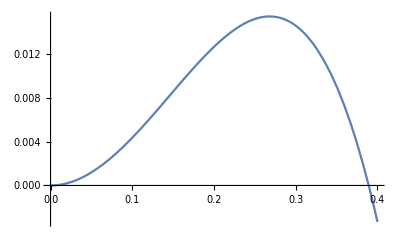

```mathematica
ρrepl2 = {zh->0.4,σc->1,ρ->0.0001,λm->-0.001,n->3,λn->1,m->4,ϵ->-0.25}
(Vboundary/.ρrepl2)
Plot[ %,{z,0,zh/.ρrepl2} ]
```

{zh→0.01,σc→1,ρ→0.0001,λm→-10,n→3,λn→10,m→4,ϵ→0.125}

-1/2 (-1+(0.0001-1.00616/z^0.5+1.7865/z^0.375)^2) z^2

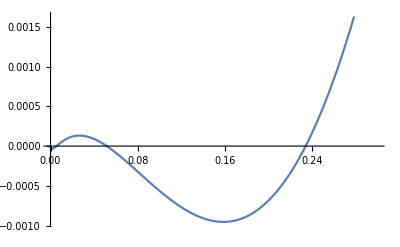

-1/2 z^2 (-1+(0.0001+10 LegendreP[0.03125,-1+(2.×10^-8)/z^4]^3-10 LegendreP[0.03125,-1+(2.×10^-8)/z^4]^4)^2)

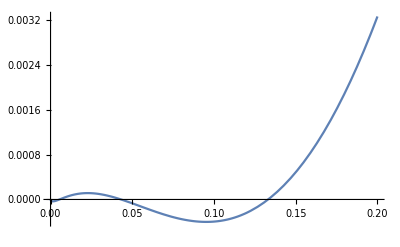

-1.×10^8 z^6-(0.0001 z^10)/(0.0001+10 LegendreP[0.03125,-1+(2.×10^-8)/z^4]^3-10 LegendreP[0.03125,-1+(2.×10^-8)/z^4]^4)+z^2 (1-(0.0001+10 LegendreP[0.03125,-1+(2.×10^-8)/z^4]^3-10 LegendreP[0.03125,-1+(2.×10^-8)/z^4]^4)^2)

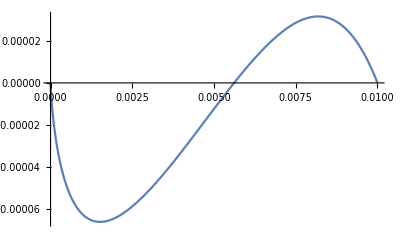

```mathematica
ρrepl2 = {zh->0.01,σc->1,ρ->0.0001,λm->-10,n->3,λn->10,m->4,ϵ->0.125}
(Vboundary/.ρrepl2)
Plot[ %,{z,0,0.3} ]
-1/2 z^2 (σ^2/σc^2-1)/.σ->ρ+ λn ϕos1type3^n+λm ϕos1type3^m/.ρrepl2
Plot[%,{z,0,0.2}]
-(z^6 4(1/(4 zh^4) -ρ/(2 σc)) - z^2 (1-((ρ+λn ϕos1type3^n+λm ϕos1type3^m)/σc)^2) + z^10 (ρ/(ρ+λn ϕos1type3^n+λm ϕos1type3^m)))/.ρrepl2
Plot[%,{z,0,zh/.ρrepl2}]
```

{zh→0.4,σc→1,ρ→0.0001,λm→-10,n→3,λn→10,m→4,ϵ→-0.125}

1/2 (1-(0.0001+14.1717 z^0.375-15.9182 z^0.5)^2) z^2

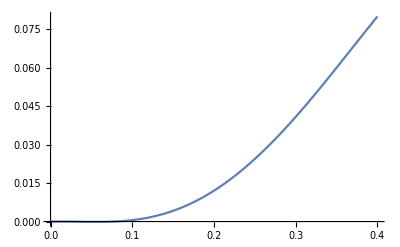

-1/2 z^2 (-1+(0.0001+10 LegendreP[-0.03125,-1+0.0512/z^4]^3-10 LegendreP[-0.03125,-1+0.0512/z^4]^4)^2)

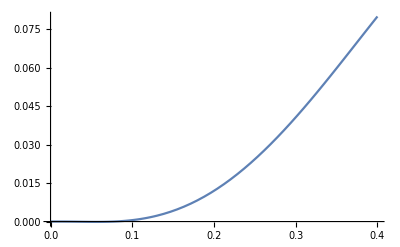

-39.0623 z^6-(0.0001 z^10)/(0.0001+10 LegendreP[-0.03125,-1+0.0512/z^4]^3-10 LegendreP[-0.03125,-1+0.0512/z^4]^4)+z^2 (1-(0.0001+10 LegendreP[-0.03125,-1+0.0512/z^4]^3-10 LegendreP[-0.03125,-1+0.0512/z^4]^4)^2)

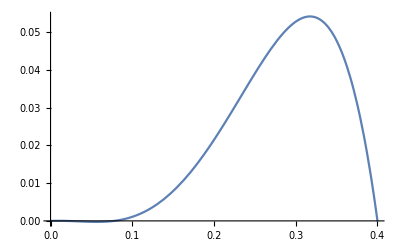

```mathematica
ρrepl2 = {zh->0.4,σc->1,ρ->0.0001,λm->-10,n->3,λn->10,m->4,ϵ->-0.125}
(Vboundary/.ρrepl2)
Plot[ %,{z,0,zh/.ρrepl2} ]
-1/2 z^2 (σ^2/σc^2-1)/.σ->ρ+ λn ϕos1type3^n+λm ϕos1type3^m/.ρrepl2
Plot[%,{z,0,zh/.ρrepl2}]
-(z^6 4(1/(4 zh^4) -ρ/(2 σc)) - z^2 (1-((ρ+λn ϕos1type3^n+λm ϕos1type3^m)/σc)^2) + z^10 (ρ/(ρ+λn ϕos1type3^n+λm ϕos1type3^m)))/.ρrepl2
Plot[%,{z,0,zh/.ρrepl2}]
```

{zh→0.4,σc→1,ρ→0.0001,λm→-10,n→3,λn→10,m→4,ϵ→-0.125}

-Graphics-

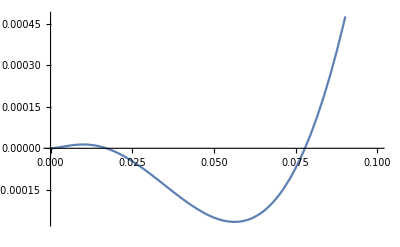

```mathematica
ρrepl2 = {zh->0.4,σc->1,ρ->0.0001,λm->-10,n->3,λn->10,m->4,ϵ->-0.125}
-(z^6 4(1/(4 zh^4) -ρ/(2 σc)) - z^2 (1-((ρ+λn ϕos1type3^n+λm ϕos1type3^m)/σc)^2) + z^10 (ρ/(ρ+λn ϕos1type3^n+λm ϕos1type3^m)))/.ρrepl2;
Plot[%,{z,0,zh/.ρrepl2}]
Plot[%%,{z,0,1/4 zh/.ρrepl2}]
```

expand near turning point

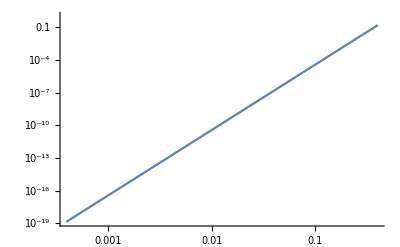

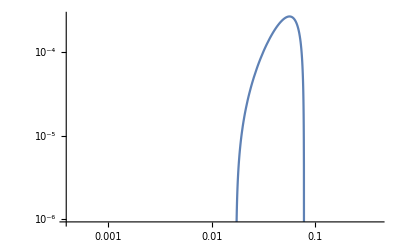

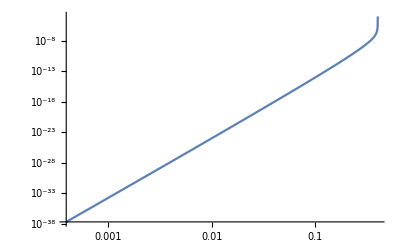

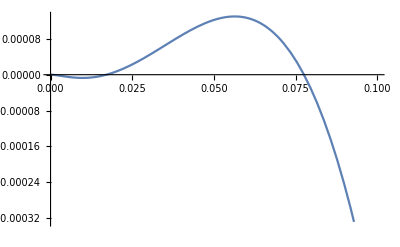

```mathematica
ρrepl2 = {zh->0.4,σc->1,ρ->0.0001,λm->-10,n->3,λn->10,m->4,ϵ->-0.125};
Vterms={-z^6 4(1/(4 zh^4) -ρ/(2 σc)),  z^2 (1-((ρ+λn ϕos1type3^n+λm ϕos1type3^m)/σc)^2) ,- z^10 (ρ/(ρ+λn ϕos1type3^n+λm ϕos1type3^m))};
LogLogPlot[-Vterms[[1]]/.ρrepl2,{z,0,zh/.ρrepl2}]
LogLogPlot[-Vterms[[2]]/.ρrepl2,{z,0,zh/.ρrepl2}]
LogLogPlot[-Vterms[[3]]/.ρrepl2,{z,0,zh/.ρrepl2}]
Plot[z^2(ρ+λn ϕos1type3^n+λm ϕos1type3^m-1)/.ρrepl2,{z,0,1/4 zh/.ρrepl2}]
```

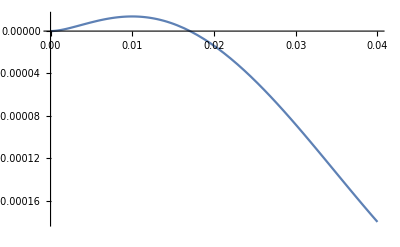

```mathematica
Plot[Vterms[[2]]/.ρrepl2,{z,0,1/10 zh/.ρrepl2}]
```

```mathematica
(*-(z^6 4(1/(4 zh^4) -ρ/(2 σc)) - z^2 (1-((ρ+λn ϕos1type3^n+λm ϕos1type3^m)/σc)^2) + z^10 (ρ/(ρ+λn ϕos1type3^n+λm ϕos1type3^m)));*)
(*Simplify[Series[Expand[ z^2 (1-((ρ+λn ϕos1type3^n+λm ϕos1type3^m)/σc)^2)]/.{m->4,n->3,ϵ->-0.1},{z,0,4}]]*)
(*Series[ϕos1type3,{z,0,2}]*)
PowerExpand[Vterms[[2]]/.ϕos1type3->(zh/z)^ϵ]
PowerExpand[Simplify[σc √(1-%/z^2)]]/.zh->1
Series[%/.ρrepl2,{z,0,2}]
Solve[%==1,z]
Solve[(%%%/.{ϵ->1,m->4,n->3})==1,z]
```

z^2 (1-((z^(-m ϵ) zh^(m ϵ) λm+z^(-n ϵ) zh^(n ϵ) λn+ρ)^2)/σc^2)

z^(-m ϵ) λm+z^(-n ϵ) λn+ρ

0.0001+10 z^0.375-10 z^0.5

{{z→0.043235},{z→0.196399}}

{{z→-1/2 √(-(4 2^(1/3) λm)/((√(729 λn^4 (-1+ρ)^2-6912 λm^3 (-1+ρ)^3)+27 λn^2 (-1+ρ))^(1/3))+(2 λn)/(√((4 2^(1/3) λm)/((√(729 λn^4 (-1+ρ)^2-6912 λm^3 (-1+ρ)^3)+27 λn^2 (-1+ρ))^(1/3))+((√(729 λn^4 (-1+ρ)^2-6912 λm^3 (-1+ρ)^3)+27 λn^2 (-1+ρ))^(1/3))/(3 2^(1/3) (-1+ρ))) (-1+ρ))-((√(729 λn^4 (-1+ρ)^2-6912 λm^3 (-1+ρ)^3)+27 λn^2 (-1+ρ))^(1/3))/(3 2^(1/3) (-1+ρ)))-1/2 √((4 2^(1/3) λm)/((√(729 λn^4 (-1+ρ)^2-6912 λm^3 (-1+ρ)^3)+27 λn^2 (-1+ρ))^(1/3))+((√(729 λn^4 (-1+ρ)^2-6912 λm^3 (-1+ρ)^3)+27 λn^2 (-1+ρ))^(1/3))/(3 2^(1/3) (-1+ρ)))},{z→1/2 √(-(4 2^(1/3) λm)/((√(729 λn^4 (-1+ρ)^2-6912 λm^3 (-1+ρ)^3)+27 λn^2 (-1+ρ))^(1/3))+(2 λn)/(√((4 2^(1/3) λm)/((√(729 λn^4 (-1+ρ)^2-6912 λm^3 (-1+ρ)^3)+27 λn^2 (-1+ρ))^(1/3))+((√(729 λn^4 (-1+ρ)^2-6912 λm^3 (-1+ρ)^3)+27 λn^2 (-1+ρ))^(1/3))/(3 2^(1/3) (-1+ρ))) (-1+ρ))-((√(729 λn^4 (-1+ρ)^2-6912 λm^3 (-1+ρ)^3)+27 λn^2 (-1+ρ))^(1/3))/(3 2^(1/3) (-1+ρ)))-1/2 √((4 2^(1/3) λm)/((√(729 λn^4 (-1+ρ)^2-6912 λm^3 (-1+ρ)^3)+27 λn^2 (-1+ρ))^(1/3))+((√(729 λn^4 (-1+ρ)^2-6912 λm^3 (-1+ρ)^3)+27 λn^2 (-1+ρ))^(1/3))/(3 2^(1/3) (-1+ρ)))},{z→-1/2 √(-(4 2^(1/3) λm)/((√(729 λn^4 (-1+ρ)^2-6912 λm^3 (-1+ρ)^3)+27 λn^2 (-1+ρ))^(1/3))-(2 λn)/(√((4 2^(1/3) λm)/((√(729 λn^4 (-1+ρ)^2-6912 λm^3 (-1+ρ)^3)+27 λn^2 (-1+ρ))^(1/3))+((√(729 λn^4 (-1+ρ)^2-6912 λm^3 (-1+ρ)^3)+27 λn^2 (-1+ρ))^(1/3))/(3 2^(1/3) (-1+ρ))) (-1+ρ))-((√(729 λn^4 (-1+ρ)^2-6912 λm^3 (-1+ρ)^3)+27 λn^2 (-1+ρ))^(1/3))/(3 2^(1/3) (-1+ρ)))+1/2 √((4 2^(1/3) λm)/((√(729 λn^4 (-1+ρ)^2-6912 λm^3 (-1+ρ)^3)+27 λn^2 (-1+ρ))^(1/3))+((√(729 λn^4 (-1+ρ)^2-6912 λm^3 (-1+ρ)^3)+27 λn^2 (-1+ρ))^(1/3))/(3 2^(1/3) (-1+ρ)))},{z→1/2 √(-(4 2^(1/3) λm)/((√(729 λn^4 (-1+ρ)^2-6912 λm^3 (-1+ρ)^3)+27 λn^2 (-1+ρ))^(1/3))-(2 λn)/(√((4 2^(1/3) λm)/((√(729 λn^4 (-1+ρ)^2-6912 λm^3 (-1+ρ)^3)+27 λn^2 (-1+ρ))^(1/3))+((√(729 λn^4 (-1+ρ)^2-6912 λm^3 (-1+ρ)^3)+27 λn^2 (-1+ρ))^(1/3))/(3 2^(1/3) (-1+ρ))) (-1+ρ))-((√(729 λn^4 (-1+ρ)^2-6912 λm^3 (-1+ρ)^3)+27 λn^2 (-1+ρ))^(1/3))/(3 2^(1/3) (-1+ρ)))+1/2 √((4 2^(1/3) λm)/((√(729 λn^4 (-1+ρ)^2-6912 λm^3 (-1+ρ)^3)+27 λn^2 (-1+ρ))^(1/3))+((√(729 λn^4 (-1+ρ)^2-6912 λm^3 (-1+ρ)^3)+27 λn^2 (-1+ρ))^(1/3))/(3 2^(1/3) (-1+ρ)))}}

{zh→0.4,σc→1,ρ→0.0001,λm→-10,n→4,λn→10,m→2,ϵ→-0.125}

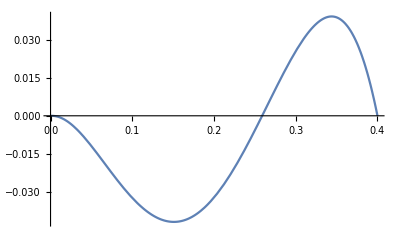

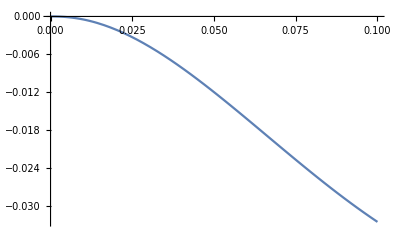

```mathematica
ρrepl2 = {zh->0.4,σc->1,ρ->0.0001,λm->-10,n->4,λn->10,m->2,ϵ->-0.125}
-(z^6 4(1/(4 zh^4) -ρ/(2 σc)) - z^2 (1-((ρ+λn ϕos1type3^n+λm ϕos1type3^m)/σc)^2) + z^10 (ρ/(ρ+λn ϕos1type3^n+λm ϕos1type3^m)))/.ρrepl2;
Plot[%,{z,0,zh/.ρrepl2}]
Plot[%%,{z,0,1/4 zh/.ρrepl2}]
```

{zh→0.4,σc→1,ρ→0.0001,λm→-10,n→3,λn→10,m→4,ϵ→-0.04}

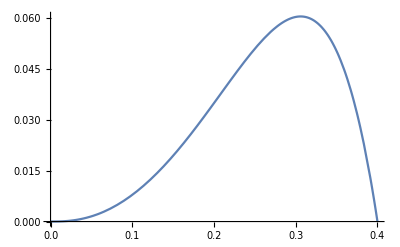

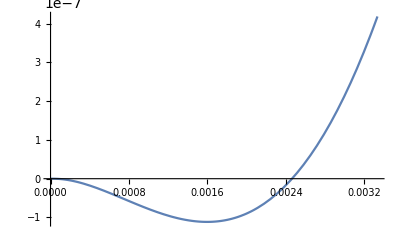

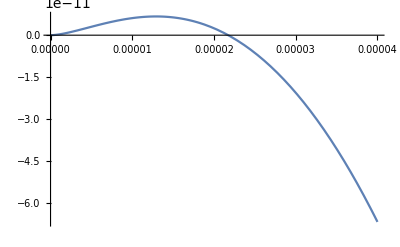

```mathematica
ρrepl2 = {zh->0.4,σc->1,ρ->0.0001,λm->-10,n->3,λn->10,m->4,ϵ->-0.04}
-(z^6 4(1/(4 zh^4) -ρ/(2 σc)) - z^2 (1-((ρ+λn ϕos1type3^n+λm ϕos1type3^m)/σc)^2) + z^10 (ρ/(ρ+λn ϕos1type3^n+λm ϕos1type3^m)))/.ρrepl2;
Plot[%,{z,0,zh/.ρrepl2}]
Plot[%%,{z,0,1/120 zh/.ρrepl2}]
Plot[%%%,{z,0,1/10000 zh/.ρrepl2}]
```

dz2==z^2 (-1+((ρ+z^(-n ϵ) zh^(n ϵ) λ Gamma[1+ϵ/4]^(-2 n) Gamma[1+ϵ/2]^n)^2)/σc^2)

-1/2 (-1+(0.0001-0.102384/z^1.)^2) z^2

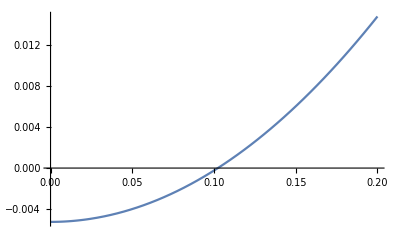

-1/2 z^2 (-1+(0.0001-10 LegendreP[0.0625,-1+(2.×10^-8)/z^4]^4)^2)

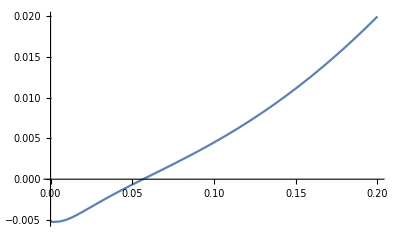

```mathematica
dz2 ==-2 Vboundary
(Vboundary/.{zh->0.01,σc->1,ρ->0.0001,λ->-10,n->4,ϵ->0.25})
Plot[ %,{z,0,0.2} ]
-1/2 z^2 (σ^2/σc^2-1)/.σ->ρ+ λ Vϕ[z,zh,n,ϵ]/.{zh->0.01,σc->1,ρ->0.0001,λ->-10,n->4,ϵ->0.25}
Plot[%,{z,0,0.2}]
```

```mathematica
Vboundary/.{zh->0.01,σc->1,ρ->0.0001,λ->1,n->4}
```

z^2 (-1+(0.0001+0.01^(4 ϵ) z^(-4 ϵ))^2)

```mathematica
Solve[(√(z^2/l^2 fm[z] + zd2)-√(z^2/l^2 fp[z] + zd2)/.{zd2->zd2+a})==z σstuff,zd2]
FullSimplify[Solve[(zd2/.%[[1]])==zd2,σstuff]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{zd2→1/(4 l^4 σstuff^2)(-4 a l^4 σstuff^2+l^4 z^2 σstuff^4-2 l^2 z^2 σstuff^2 fm[z]+z^2 fm[z]^2-2 l^2 z^2 σstuff^2 fp[z]-2 z^2 fm[z] fp[z]+z^2 fp[z]^2)}}

{{σstuff→-√((2 (a+zd2))/z^2+(fm[z]+fp[z])/l^2-(2 √(l^4 (l^2 (a+zd2)+z^2 fm[z]) (l^2 (a+zd2)+z^2 fp[z])))/(l^4 z^2))},{σstuff→√((2 (a+zd2))/z^2+(fm[z]+fp[z])/l^2-(2 √(l^4 (l^2 (a+zd2)+z^2 fm[z]) (l^2 (a+zd2)+z^2 fp[z])))/(l^4 z^2))},{σstuff→-√((2 (a+zd2))/z^2+(fm[z]+fp[z])/l^2+(2 √(l^4 (l^2 (a+zd2)+z^2 fm[z]) (l^2 (a+zd2)+z^2 fp[z])))/(l^4 z^2))},{σstuff→√((2 (a+zd2))/z^2+(fm[z]+fp[z])/l^2+(2 √(l^4 (l^2 (a+zd2)+z^2 fm[z]) (l^2 (a+zd2)+z^2 fp[z])))/(l^4 z^2))}}

```mathematica
Solve[λn ϕ^n+ λm ϕ^m + (σc-ρ)==0,ϕ]
```

$Aborted

```mathematica
PowerExpand[Solve[(λ3 ϕ^4-λ2 ϕ^2 - (σc - ρ))==0,ϕ]]
PowerExpand[Solve[ϕ^4-2 √(σc -ρ)ϕ^2 -ρ==-σc,ϕ]]
```

{{ϕ→-(√(λ2/λ3-(√(λ2^2-4 λ3 ρ+4 λ3 σc))/λ3))/(√2)},{ϕ→(√(λ2/λ3-(√(λ2^2-4 λ3 ρ+4 λ3 σc))/λ3))/(√2)},{ϕ→-(√(λ2/λ3+(√(λ2^2-4 λ3 ρ+4 λ3 σc))/λ3))/(√2)},{ϕ→(√(λ2/λ3+(√(λ2^2-4 λ3 ρ+4 λ3 σc))/λ3))/(√2)}}

{{ϕ→-(-ρ+σc)^(1/4)},{ϕ→-(-ρ+σc)^(1/4)},{ϕ→(-ρ+σc)^(1/4)},{ϕ→(-ρ+σc)^(1/4)}}

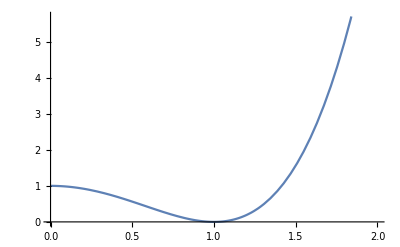

```mathematica
Plot[z^4-2 z^2+1,{z,0,2}]
```

{zh→0.4,σc→1,ρ→0.0001,λm→-10,n→4,λn→10,m→2,ϵ→-0.125}

-1/2 (-1+(0.0001+6.32456/z^0.5-7.95271/z^0.25)^2) z^2

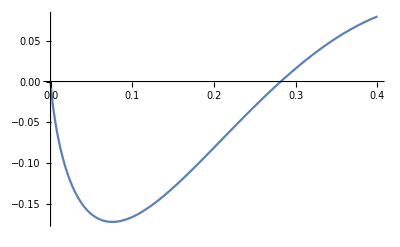

```mathematica
(*ρrepl2 = {zh->1,σc->0.1,ρ->0.001,λn->-10,n->4,λm->20 √(0.1-0.001),m->3,ϵ->0.01}*)
ρrepl2 = {zh->0.4,σc->1,ρ->0.0001,λm->-10,n->4,λn->10,m->2,ϵ->-0.125}
-1/2 z^2 (σ^2/σc^2-1)/.σ->ρ+ λn (z/zh)^(ϵ n)+λm (z/zh)^(ϵ m)/.ρrepl2
Plot[%,{z,0,zh/.ρrepl2}]
```

{zh→0.4,σc→1,ρ→0.0001,λm→-10,n→4,λn→10,m→2,ϵ→-0.125}

-Graphics-

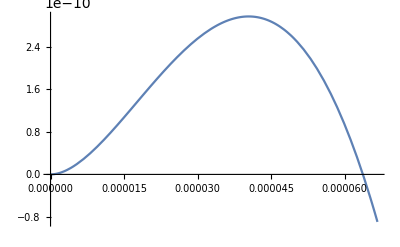

```mathematica
(*ρrepl2 = {zh->0.1,σc->1,ρ->0.001,λn->-10,n->4,λm->-10,m->2,ϵ->-0.125}*)
ρrepl2 = {zh->0.4,σc->1,ρ->0.0001,λm->-10,n->4,λn->10,m->2,ϵ->-0.125}
-(z^6 4(1/(4 zh^4) -ρ/(2 σc)) - z^2 (1-((ρ+λn ϕos1type3^n+λm ϕos1type3^m)/σc)^2) + z^10 (ρ/(ρ+λn ϕos1type3^n+λm ϕos1type3^m)))/.ρrepl2;
Plot[%,{z,0,zh/.ρrepl2}]
Plot[%%,{z,0,1/6000 zh/.ρrepl2}]
```

```mathematica
NDSolve[{z'[τ]==-(z^6 4(1/(4 zh^4) -ρ/(2 σc)) - z^2 (1-((ρ+λn ϕos1type3^n+λm ϕos1type3^m)/σc)^2) + z^10 (ρ/(ρ+λn ϕos1type3^n+λm ϕos1type3^m))/.z->z[τ])^(1/2)/.ρrepl2,z[0]==0.2 },z[τ],{τ,0,10}]
```

NDSolve::ndnco: The number of constraints (0) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (1).

NDSolve[z'[τ]==√(-((1-(0.0001-10 LegendreP[-0.03125,-1+0.0512/z[τ]^4]^2+10 LegendreP[-0.03125,-1+0.0512/z[τ]^4]^4)^2) z[τ]^2)+39.0623 z[τ]^6+(0.0001 z[τ]^10)/(0.0001-10 LegendreP[-0.03125,-1+0.0512/z[τ]^4]^2+10 LegendreP[-0.03125,-1+0.0512/z[τ]^4]^4)),z[τ],{τ,0,10}]

```mathematica
{ρM ->zh^-4 A }
exparg = zh ρM (1-(1-ρω/ρM)^(3/4))/.%
```

{ρM→A/zh^4}

(A (1-(1-(zh^4 ρω)/A)^(3/4)))/zh^3

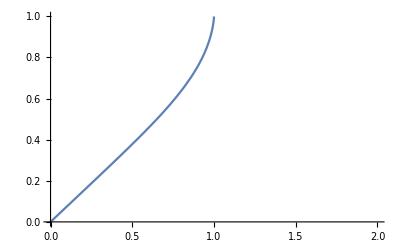

```mathematica
Plot[z^-3(1-(1-a z^4)^(3/4))/.a->1,{z,0,2}]
```

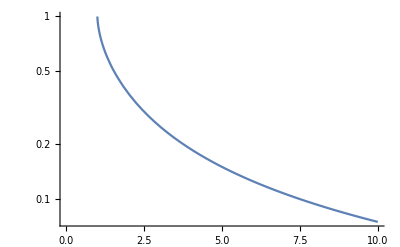

```mathematica
LogPlot[z^-3(1-(1-a z^4)^(3/4))/.{z->1/T,a->1},{T,0,10}]
```